# Spiral Repellor

## Full Case: Non-Compact Phase Spaces

### Non-Compact x - z Phase Space

```mathematica
(*Define the parameters for this case*)
wx=-0.5;
q=1;
ϵ=-0.25;
ℛ=0.05;
```

```mathematica
(*Define the dynamical system for coupled dark matter (z) and dark energy (x)*)
dex:=x'=-3*(x-ℛ)*(1+wx+ϵ*x)-q*x*z
dez:=z'=-3*z + q*x*z
```

```mathematica
(*Find the fixed points of the system*)
FPs=Solve[{dex==0,dez==0},{x,z}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{x→0.05,z→0.},{x→2.,z→0.},{x→3.,z→0.7375}}

```mathematica
FP[1]={x/.FPs[[1,1]],z/.FPs[[1,2]]};
FP[2]={x/.FPs[[2,1]],z/.FPs[[2,2]]};
FP[3]={x/.FPs[[3,1]],z/.FPs[[3,2]]};
```

```mathematica
(*Put fixed points into a table*)
FPs=Table[FP[i],{i,1,3}];
```

```mathematica
(*Find the 4D Jacobian matrix for general system of equations. D[] differentiates each expression*)
J=Simplify[{{D[dex,x],D[dex,z]}, {D[dez,x],D[dez,z]}}];
J//MatrixForm
```

(-1.5375+1.5 x-1. z | -x
z | -3+x)

```mathematica
(*Find the Jacobian and eigenvalues for each fixed point*)
FPTable=Table[{FPs[[i]]//MatrixForm,Simplify[J/.{x->FPs[[i,1]],z->FPs[[i,2]]}]//MatrixForm,Eigenvalues[J/.{x->FPs[[i,1]],z->FPs[[i,2]]}]//MatrixForm,Eigenvectors[J/.{x->FPs[[i,1]],z->FPs[[i,2]]}]//MatrixForm},{i,1,3}];
```

```mathematica
(*Use TableForm to display the fixed points with their Jacobian matrix and eigenvalues*)
FPTable=TableForm[FPTable,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

Fixed Point | Jacobian | Eigenvalues | Eigenvectors
(0.05
0.) | (-1.4625 | -0.05
0. | -2.95) | (-2.95
-1.4625) | (0.0335945 | 0.999436
1. | 0.)
(2.
0.) | (1.4625 | -2.
0. | -1.) | (1.4625
-1.) | (1. | 0.
0.630444 | 0.776235)
(3.
0.7375) | (2.225 | -3.
0.7375 | 0.) | (1.1125+0.987342 ⅈ
1.1125-0.987342 ⅈ) | (0.895922+0. ⅈ | 0.332238-0.29486 ⅈ
0.895922+0. ⅈ | 0.332238+0.29486 ⅈ)

```mathematica
(*Plot the fixed points*)
FPShowxz=ListPlot[FPs,PlotStyle->Black];
```

```mathematica
(*Define the differential equations in terms of their variables*)
DE=dex;
DM=dez;
```

```mathematica
PhaseSpacexz=StreamPlot[{DE,DM},{x,-1,5},{z,0,3},FrameLabel->{"x","z"}];
```

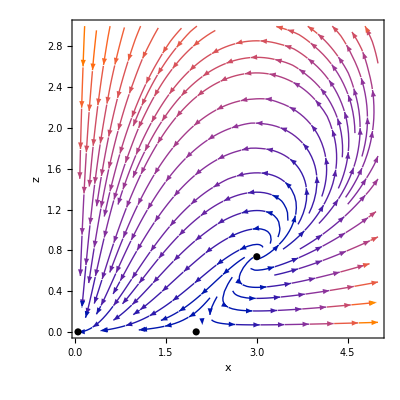

```mathematica
Show[PhaseSpacexz,FPShowxz]
```

```mathematica
(*Define the dynamical system for coupled dark matter (z) and dark energy (x)*)
de1:=x'=-3*y*(x-ℛ)*(1+wx+ϵ*x)-q*x*y*z
de2:=y'=-y^2-(1/6)*(z+x*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*x^2) 
de3:=z'=-3*y*z + q*x*y*z
```

```mathematica
(*Find the fixed points of the system*)
FPs=Solve[{de1==0,de2==0,de3==0},{x,y,z}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Solve::svars: Equations may not give solutions for all "solve" variables.

{{y→0.,z→0.0125 (6.+37. x+60. x^2)},{x→0.05,y→-0.129099,z→0.},{x→0.05,y→0.129099,z→0.},{x→2.,y→-0.816497,z→0.},{x→2.,y→0.816497,z→0.},{x→3.,y→-1.11617,z→0.7375},{x→3.,y→1.11617,z→0.7375}}

```mathematica
(*Remove arrows from fixed points and put them into a common variable name*)
FP[1]={x,y/.FPs[[1,1]],z/.FPs[[1,2]]};
FP[2]={x/.FPs[[2,1]],y/.FPs[[2,2]],z/.FPs[[2,3]]};
FP[3]={x/.FPs[[3,1]],y/.FPs[[3,2]],z/.FPs[[3,3]]};
FP[4]={x/.FPs[[4,1]],y/.FPs[[4,2]],z/.FPs[[4,3]]};
FP[5]={x/.FPs[[5,1]],y/.FPs[[5,2]],z/.FPs[[5,3]]};
FP[6]={x/.FPs[[6,1]],y/.FPs[[6,2]],z/.FPs[[6,3]]};
FP[7]={x/.FPs[[7,1]],y/.FPs[[7,2]],z/.FPs[[7,3]]};
```

```mathematica
(*Put fixed points into a table*)
FPs=Table[FP[i],{i,1,6}];
```

```mathematica
(*Find the 4D Jacobian matrix for general system of equations. D[] differentiates each expression*)
J=Simplify[{{D[de1,x],D[de1,y],D[de1,z]}, {D[de2,x],D[de2,y],D[de2,z]},{D[de3,x],D[de3,y],D[de3,z]}}];
J//MatrixForm
```

(y (-1.5375+1.5 x-1. z) | 0.075+0.75 x^2-1. x (1.5375+z) | -x y
0.0770833+0.25 x | -2 y | -1/6
y z | (-3+x) z | (-3+x) y)

```mathematica
(*Find the Jacobian and eigenvalues for each fixed point*)
FPTable=Table[{FPs[[i]]//MatrixForm,Simplify[J/.{x->FPs[[i,1]],y->FPs[[i,2]],z->FPs[[i,3]]}]//MatrixForm,Eigenvalues[J/.{x->FPs[[i,1]],y->FPs[[i,2]],z->FPs[[i,3]]}]//MatrixForm,Eigenvectors[J/.{x->FPs[[i,1]],y->FPs[[i,2]],z->FPs[[i,3]]}]//MatrixForm},{i,1,6}];
```

```mathematica
(*Use TableForm to display the fixed points with their Jacobian matrix and eigenvalues*)
FPTable=TableForm[FPTable,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

Fixed Point | Jacobian | Eigenvalues | Eigenvectors
(x
0.
0.0125 (6.+37. x+60. x^2)) | (0. | 0.075-1.6125 x+0.2875 x^2-0.75 x^3 | 0.
0.0770833+0.25 x | 0. | -1/6
0. | -0.225-1.3125 x-1.7875 x^2+0.75 x^3 | 0.) | (0
-√(0.0432812+0.113203 x-0.0830469 x^2-0.110937 x^3-0.1875 x^4)
√(0.0432812+0.113203 x-0.0830469 x^2-0.110937 x^3-0.1875 x^4)) | (0.666667/(0.308333+1. x) | 0 | 1.
-(1. (-0.0308333+0.562917 x+2.03181 x^2-0.075 x^3+1. x^4))/((0.308333+1. x) (-0.3-1.75 x-2.38333 x^2+1. x^3)) | -(1.33333 √(0.0432813+0.113203 x-0.0830469 x^2-0.110938 x^3-0.1875 x^4))/(-0.3-1.75 x-2.38333 x^2+1. x^3) | 1.
-(1. (-0.0308333+0.562917 x+2.03181 x^2-0.075 x^3+1. x^4))/((0.308333+1. x) (-0.3-1.75 x-2.38333 x^2+1. x^3)) | (1.33333 √(0.0432813+0.113203 x-0.0830469 x^2-0.110938 x^3-0.1875 x^4))/(-0.3-1.75 x-2.38333 x^2+1. x^3) | 1.)
(0.05
-0.129099
0.) | (0.188808 | 0. | 0.00645497
0.0895833 | 0.258199 | -1/6
0. | 0. | 0.380843) | (0.380843
0.258199
0.188808) | (0.0201538 | -0.800065 | 0.599574
0. | 1. | 0.
0.612372 | -0.790569 | 0.)
(0.05
0.129099
0.) | (-0.188808 | 0. | -0.00645497
0.0895833 | -0.258199 | -1/6
0. | 0. | -0.380843) | (-0.380843
-0.258199
-0.188808) | (0.0201538 | 0.800065 | 0.599574
0. | 1. | 0.
0.612372 | 0.790569 | 0.)
(2.
-0.816497
0.) | (-1.19413 | 0. | 1.63299
0.577083 | 1.63299 | -1/6
0. | 0. | 0.816497) | (1.63299
-1.19413
0.816497) | (0. | 1. | 0.
0.979796 | -0.2 | 0.
0.605959 | -0.275985 | 0.746087)
(2.
0.816497
0.) | (1.19413 | 0. | -1.63299
0.577083 | -1.63299 | -1/6
0. | 0. | -0.816497) | (-1.63299
1.19413
-0.816497) | (0. | 1. | 0.
0.979796 | 0.2 | 0.
0.605959 | 0.275985 | 0.746087)
(3.
-1.11617
0.7375) | (-2.48348 | -8.88178×10^-16 | 3.34851
0.827083 | 2.23234 | -1/6
-0.823175 | 0. | 0.) | (2.23234+0. ⅈ
-1.24174+1.10204 ⅈ
-1.24174-1.10204 ⅈ) | (-8.17767×10^-17+0. ⅈ | 1.+0. ⅈ | 1.5283×10^-16+0. ⅈ
0.880401+0. ⅈ | -0.180212-0.0432659 ⅈ | 0.326482+0.289752 ⅈ
0.880401+0. ⅈ | -0.180212+0.0432659 ⅈ | 0.326482-0.289752 ⅈ)

```mathematica
Eq1=de1;
Eq2=de2;
Eq3=de3;
```

```mathematica
PhaseSpacexyz=StreamPlot3D[{Eq1,Eq2,Eq3},{x,0,15},{y,-5,5},{z,0,10},AxesLabel->{"x","y","z"},StreamMarkers->"Arrow"]
```

-Graphics3D-

## Full Case: Compactification

### Compact x - z Phase Space

```mathematica
wx=-0.5;
q=1;
ϵ=-0.25;
ℛ=0.05;
```

```mathematica
(*Define the dynamical system for coupled dark matter (z) and dark energy (x)*)
deX:=X'=-3*(X-ℛ*(1-X))*((1+wx)*(1-X)+ϵ*X)-q*X*(1-X)*Z/(1-Z)
deZ:=Z'=-3*Z*(1-Z) + q*(X/(1-X))*Z*(1-Z)
```

```mathematica
deX/.X->0
```

0.075

```mathematica
(*Find the fixed points of the system*)
FPs=Solve[{deX==0,deZ==0},{X,Z}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{X→0.047619,Z→0.},{X→0.666667,Z→0.},{X→0.75,Z→0.42446}}

```mathematica
FP[1]={X/.FPs[[1,1]],Z/.FPs[[1,2]]};
FP[2]={X/.FPs[[2,1]],Z/.FPs[[2,2]]};
FP[3]={X/.FPs[[3,1]],Z/.FPs[[3,2]]};
```

```mathematica
(*Put fixed points into a table*)
FPs=Table[FP[i],{i,1,3}];
```

```mathematica
(*Find the 4D Jacobian matrix for general system of equations. D[] differentiates each expression*)
J=Simplify[{{D[deX,X],D[deX,Z]}, {D[deZ,X],D[deZ,Z]}}];
J//MatrixForm
```

((1.6875-0.6875 Z+X (-4.725+2.725 Z))/(-1.+Z) | ((-1+X) X)/(-1+Z)^2
-((-1+Z) Z)/(-1+X)^2 | ((-3+4 X) (-1+2 Z))/(-1+X))

```mathematica
(*Find the Jacobian and eigenvalues for each fixed point*)
FPTable=Table[{FPs[[i]]//MatrixForm,Simplify[J/.{X->FPs[[i,1]],Z->FPs[[i,2]]}]//MatrixForm,Eigenvalues[J/.{X->FPs[[i,1]],Z->FPs[[i,2]]}]//MatrixForm,Eigenvectors[J/.{X->FPs[[i,1]],Z->FPs[[i,2]]}]//MatrixForm},{i,1,3}];
```

```mathematica
(*Use TableForm to display the fixed points with their Jacobian matrix and eigenvalues*)
(*Extra fixed points from compactification at {X = 1, Z = 0},{X = 1, Z = 1},{X = 0, Z = 1}*)
FPTable=TableForm[FPTable,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

Fixed Point | Jacobian | Eigenvalues | Eigenvectors
(0.047619
0.) | (-1.4625 | -0.0453515
0. | -2.95) | (-2.95
-1.4625) | (0.0304742 | 0.999536
1. | 0.)
(0.666667
0.) | (1.4625 | -0.222222
0. | -1.) | (1.4625
-1.) | (1. | 0.
0.0898773 | 0.995953)
(0.75
0.42446) | (2.225 | -0.566045
3.9087 | 0.) | (1.1125+0.987342 ⅈ
1.1125-0.987342 ⅈ) | (0.266011+0.236084 ⅈ | 0.934613+0. ⅈ
0.266011-0.236084 ⅈ | 0.934613+0. ⅈ)

```mathematica
FPShowCompactxz=ListPlot[FPs,PlotStyle->Black];
```

```mathematica
(*Define the differential equations in terms of their variables*)
DE=deX;
DM=deZ;
```

```mathematica
PhaseSpaceCompactxz=StreamPlot[{DE,DM},{X,-0.1,1},{Z,0,1},FrameLabel->{"X","Z"}];
```

```mathematica
x0=ContourPlot[x==0,{x,-0.1,0.1},{z,0,1},ContourStyle->Black];
```

```mathematica
zEqn=-3*(X-ℛ*(1-X))*((1+wx)*(1-X)+ϵ*X)/(q*X*(1-X))
```

-(3 (0.5 (1-X)-0.25 X) (-0.05 (1-X)+X))/((1-X) X)

```mathematica
ZLine=Plot[zEqn/(1+zEqn),{X,0,1},PlotStyle->Blue];
```

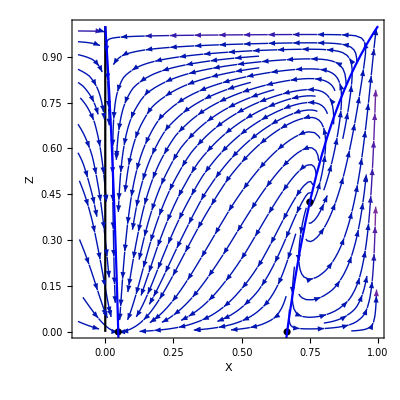

```mathematica
Show[PhaseSpaceCompactxz,FPShowCompactxz,x0,ZLine]
```

```mathematica
(*As long as the dark energy density is initially positive, it will not become negative*)
(*The dark energy density can become less than ℛ*)
```

```mathematica
deX/.{X->0.0001,Z->0.99999}
```

-9.92407

```mathematica
deX/.{X->-0.0001,Z->0.99999}
```

10.0761

```mathematica
deX/.{X->0,Z->0.99999}
```

0.075

### Compact x - y - z Phase Space

```mathematica
(*Define the parameters for this case*)
wx=-0.5;
q=1;
ϵ=-0.25;
ℛ=0.05;
```

```mathematica
(*Define the dynamical system for compact interacting dark matter (Z) and dark energy (X)*)
```

```mathematica
deX:=X'=-3*(Y/((1-Y^2)^(1/2)))*(X-ℛ*(1-X))*((1+wx)*(1-X)+ϵ*X)-q*X*(1-X)*(Z/(1-Z))*(Y/((1-Y^2)^(1/2)))
deY:=Y'=-Y^2*(1-Y^2)^(1/2)-(((1-Y^2)^(3/2))/6)*((Z/(1-Z))+(X/(1-X))*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*X^2/((1-X)^2))
deZ:=Z'=-3*Z*(1-Z)*(Y/((1-Y^2)^(1/2))) + q*(X/(1-X))*Z*(1-Z)*(Y/((1-Y^2)^(1/2)))
```

```mathematica
(*Find the fixed points of the system*)
FPs=Solve[{deX==0,deY==0,deZ==0},{X,Y,Z}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{Y→0.,Z→(6.+25. X+29. X^2)/(86.-135. X+109. X^2)},{X→0.666667,Y→-0.632456,Z→0.},{X→0.047619,Y→-0.128037,Z→0.},{X→-0.431034-0.145278 ⅈ,Y→0.,Z→0.},{X→-0.431034+0.145278 ⅈ,Y→0.,Z→0.},{X→0.047619,Y→0.128037,Z→0.},{X→0.666667,Y→0.632456,Z→0.},{X→0.75,Y→-0.744803,Z→0.42446},{X→0.75,Y→0.744803,Z→0.42446},{X→0.75,Y→0.,Z→0.891452}}

```mathematica
(*Remove arrows from fixed points and put them into a common variable name*)
FP[1]={X,Y/.FPs[[1,1]],Z/.FPs[[1,2]]};
FP[2]={X/.FPs[[2,1]],Y/.FPs[[2,2]],Z/.FPs[[2,3]]};
FP[3]={X/.FPs[[3,1]],Y/.FPs[[3,2]],Z/.FPs[[3,3]]};
FP[4]={X/.FPs[[6,1]],Y/.FPs[[6,2]],Z/.FPs[[6,3]]};
FP[5]={X/.FPs[[7,1]],Y/.FPs[[7,2]],Z/.FPs[[7,3]]};
FP[6]={X/.FPs[[8,1]],Y/.FPs[[8,2]],Z/.FPs[[8,3]]};
FP[7]={X/.FPs[[9,1]],Y/.FPs[[9,2]],Z/.FPs[[9,3]]};
FP[8]={X/.FPs[[10,1]],Y/.FPs[[10,2]],Z/.FPs[[10,3]]};
```

```mathematica
(*Put fixed points into a table*)
FPs=Table[FP[i],{i,1,8}];
```

```mathematica
(*Plot fixed points*)
FPsXYZ=ListPointPlot3D[FPs,PlotStyle->Black];
```

```mathematica
(*Find the 4D Jacobian matrix for general system of equations. D[] differentiates each expression*)
J=Simplify[{{D[deX,X],D[deX,Y],D[deX,Z]},{D[deY,X],D[deY,Y],D[deY,Z]},{D[deZ,X],D[deZ,Y],D[deZ,Z]}}];
J//MatrixForm
```

((Y (1.6875-0.6875 Z+X (-4.725+2.725 Z)))/(√(1-Y^2) (-1.+Z)) | (0.075+X^2 (2.3625-1.3625 Z)+X (-1.6875+0.6875 Z)-0.075 Z)/(√(1-Y^2) (-1.+Y^2) (-1.+Z)) | ((-1+X) X Y)/(√(1-Y^2) (-1+Z)^2)
(0.172917 (0.445783+1. X) √(1-Y^2) (-1.+Y^2))/(-1.+X)^3 | (Y (2.0375-2.5375 Z+Y^2 (-3.0375+3.5375 Z)+X (-3.84375+Y^2 (5.84375-6.84375 Z)+4.84375 Z)+X^2 (2.18125-2.68125 Z+Y^2 (-3.18125+3.68125 Z))))/((-1.+X)^2 √(1-Y^2) (-1.+Z)) | -((1-Y^2)^(3/2))/(6 (-1+Z)^2)
-(Y (-1+Z) Z)/((-1+X)^2 √(1-Y^2)) | ((-3+4 X) (-1+Z) Z)/((-1+X) (1-Y^2)^(3/2)) | ((-3+4 X) Y (-1+2 Z))/((-1+X) √(1-Y^2)))

```mathematica
(*Find the Jacobian and eigenvalues for each fixed point*)
FPTable=Table[{FPs[[i]]//MatrixForm,Simplify[J/.{X->FPs[[i,1]],Y->FPs[[i,2]],Z->FPs[[i,3]]}]//MatrixForm,Eigenvalues[J/.{X->FPs[[i,1]],Y->FPs[[i,2]],Z->FPs[[i,3]]}]//MatrixForm,Eigenvectors[J/.{X->FPs[[i,1]],Y->FPs[[i,2]],Z->FPs[[i,3]]}]//MatrixForm},{i,1,8}];
```

```mathematica
(*Use TableForm to display the fixed points with their Jacobian matrix and eigenvalues*)
(*Extra fixed points from compactification at {X = 1, Z = 0},{X = 1, Z = 1},{X = 0, Z = 1}*)
FPTable=TableForm[FPTable,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

Fixed Point | Jacobian | Eigenvalues | Eigenvectors
(X
0.
(6.+25. X+29. X^2)/(86.-135. X+109. X^2)) | (0. | (0.075-1.9125 X+5.575 X^2-6.4625 X^3+2.725 X^4)/(1.-2. X+1. X^2) | 0.
(-0.0770833-0.172917 X)/(-1.+X)^3 | 0. | -(0.309401 (0.788991-1.23853 X+1. X^2)^2)/((1.-2. X+1. X^2)^2)
0. | (0.121202+0.101002 X-0.653144 X^2-0.262604 X^3+1.47462 X^4-0.781079 X^5)/((-1.+X) (0.788991-1.23853 X+1. X^2)^2) | 0.) | (0
-(√(2.36752×10^6-3.23487×10^7 X+2.03048×10^8 X^2-7.61682×10^8 X^3+1.80853×10^9 X^4-2.3693×10^9 X^5-5.96589×10^8 X^6+1.13797×10^10 X^7-3.17438×10^10 X^8+5.67742×10^10 X^9-7.55941×10^10 X^10+7.849×10^10 X^11-6.45121×10^10 X^12+4.19172×10^10 X^13-2.12178×10^10 X^14+8.11413×10^9 X^15-2.21527×10^9 X^16+3.86202×10^8 X^17-3.24002×10^7 X^18))/((-1.+X)^4 √(1.-2. X+1. X^2) (86.-135. X+109. X^2)^2)
(√(2.36752×10^6-3.23487×10^7 X+2.03048×10^8 X^2-7.61682×10^8 X^3+1.80853×10^9 X^4-2.3693×10^9 X^5-5.96589×10^8 X^6+1.13797×10^10 X^7-3.17438×10^10 X^8+5.67742×10^10 X^9-7.55941×10^10 X^10+7.849×10^10 X^11-6.45121×10^10 X^12+4.19172×10^10 X^13-2.12178×10^10 X^14+8.11413×10^9 X^15-2.21527×10^9 X^16+3.86202×10^8 X^17-3.24002×10^7 X^18))/((-1.+X)^4 √(1.-2. X+1. X^2) (86.-135. X+109. X^2)^2)) | (-(1.78931 (-1.+X)^3 (0.788991-1.23853 X+1. X^2)^2)/((0.445783+1. X) (1.-2. X+1. X^2)^2) | 0 | 1.
-(1. (-0.0165874+0.606034 X-6.81355 X^2+40.8788 X^3-153.503 X^4+370.935 X^5-488.211 X^6-216.371 X^7+2925.39 X^8-8444.38 X^9+15943.1 X^10-22619.1 X^11+25232.4 X^12-22502.4 X^13+16080.6 X^14-9133.98 X^15+4046.6 X^16-1351.95 X^17+321.135 X^18-48.4237 X^19+3.48876 X^20))/((-1.+1. X)^6 (-0.75+1. X) (0.445783+1. X) (1.-2. X+1. X^2)^2 (0.788991-1.23853 X+1. X^2)^2 (0.206897+0.862069 X+1. X^2)) | ((0.+4.20932×10^-7 ⅈ) √(-2.48252×10^12+3.39201×10^13 X-2.12911×10^14 X^2+7.98682×10^14 X^3-1.89638×10^15 X^4+2.48439×10^15 X^5+6.25569×10^14 X^6-1.19325×10^16 X^7+3.32858×10^16 X^8-5.95321×10^16 X^9+7.92661×10^16 X^10-8.23027×10^16 X^11+6.76458×10^16 X^12-4.39534×10^16 X^13+2.22485×10^16 X^14-8.50829×10^15 X^15+2.32288×10^15 X^16-4.04963×10^14 X^17+3.39741×10^13 X^18))/((-1.+X)^3 (-1.+1. X) (-3.+4. X) (1.-2. X+1. X^2) (0.206897+0.862069 X+1. X^2)) | 1.
-(1. (-0.0165874+0.606034 X-6.81355 X^2+40.8788 X^3-153.503 X^4+370.935 X^5-488.211 X^6-216.371 X^7+2925.39 X^8-8444.38 X^9+15943.1 X^10-22619.1 X^11+25232.4 X^12-22502.4 X^13+16080.6 X^14-9133.98 X^15+4046.6 X^16-1351.95 X^17+321.135 X^18-48.4237 X^19+3.48876 X^20))/((-1.+1. X)^6 (-0.75+1. X) (0.445783+1. X) (1.-2. X+1. X^2)^2 (0.788991-1.23853 X+1. X^2)^2 (0.206897+0.862069 X+1. X^2)) | -((0.+4.20932×10^-7 ⅈ) √(-2.48252×10^12+3.39201×10^13 X-2.12911×10^14 X^2+7.98682×10^14 X^3-1.89638×10^15 X^4+2.48439×10^15 X^5+6.25569×10^14 X^6-1.19325×10^16 X^7+3.32858×10^16 X^8-5.95321×10^16 X^9+7.92661×10^16 X^10-8.23027×10^16 X^11+6.76458×10^16 X^12-4.39534×10^16 X^13+2.22485×10^16 X^14-8.50829×10^15 X^15+2.32288×10^15 X^16-4.04963×10^14 X^17+3.39741×10^13 X^18))/((-1.+X)^3 (-1.+1. X) (-3.+4. X) (1.-2. X+1. X^2) (0.206897+0.862069 X+1. X^2)) | 1.)
(0.666667
-0.632456
0.) | (-1.19413 | 0. | 0.181444
2.41384 | 1.63299 | -0.0774597
0. | 0. | 0.816497) | (1.63299
-1.19413
0.816497) | (0. | 1. | 0.
0.760506 | -0.649331 | 0.
0.0885881 | -0.168767 | 0.981667)
(0.047619
-0.128037
0.) | (0.188808 | 2.84523×10^-17 | 0.00585485
0.0963469 | 0.258199 | -0.162585
0. | 0. | 0.380843) | (0.380843
0.258199
0.188808) | (0.0185705 | -0.792875 | 0.609102
-6.61074×10^-16 | -1. | 0.
-0.584422 | 0.81145 | 0.)
(0.047619
0.128037
0.) | (-0.188808 | 2.84523×10^-17 | -0.00585485
0.0963469 | -0.258199 | -0.162585
0. | 0. | -0.380843) | (-0.380843
-0.258199
-0.188808) | (0.0185705 | 0.792875 | 0.609102
-6.61074×10^-16 | 1. | 0.
0.584422 | 0.81145 | 0.)
(0.666667
0.632456
0.) | (1.19413 | 0. | -0.181444
2.41384 | -1.63299 | -0.0774597
0. | 0. | -0.816497) | (-1.63299
1.19413
-0.816497) | (0. | 1. | 0.
0.760506 | 0.649331 | 0.
0.0885881 | 0.168767 | 0.981667)
(0.75
-0.744803
0.42446) | (-2.48348 | 0. | 0.631802
3.9319 | 2.23234 | -0.149497
-4.36277 | 0. | 0.) | (2.23234+0. ⅈ
-1.24174+1.10204 ⅈ
-1.24174-1.10204 ⅈ) | (0.+0. ⅈ | 1.+0. ⅈ | 0.+0. ⅈ
0.25061-0.222416 ⅈ | -0.29583+0.157884 ⅈ | 0.880502+0. ⅈ
0.25061+0.222416 ⅈ | -0.29583-0.157884 ⅈ | 0.880502+0. ⅈ)
(0.75
0.744803
0.42446) | (2.48348 | 0. | -0.631802
3.9319 | -2.23234 | -0.149497
4.36277 | 0. | 0.) | (-2.23234+0. ⅈ
1.24174+1.10204 ⅈ
1.24174-1.10204 ⅈ) | (0.+0. ⅈ | 1.+0. ⅈ | 0.+0. ⅈ
0.25061+0.222416 ⅈ | 0.29583+0.157884 ⅈ | 0.880502+0. ⅈ
0.25061-0.222416 ⅈ | 0.29583-0.157884 ⅈ | 0.880502+0. ⅈ)
(0.75
0.
0.891452) | (0. | -1.40156 | 0.
13.2333 | 0. | -14.145
0. | 0. | 0.) | (0.+4.30666 ⅈ
0.-4.30666 ⅈ
0.+0. ⅈ) | (0.-0.309465 ⅈ | -0.950911+0. ⅈ | 0.+0. ⅈ
0.+0.309465 ⅈ | -0.950911+0. ⅈ | 0.+0. ⅈ
0.730249+0. ⅈ | 0.+0. ⅈ | 0.683182+0. ⅈ)

```mathematica
(*Plot the fixed points of the system*)
FPShow=ListPointPlot3D[Table[FP[i],{i,2,8}], PlotStyle->{Black}];
```

```mathematica
(*Plot the fixed points from compactification*)
CompactFPShow=ListPointPlot3D[{{1,1,1},{1,-1,1},{0,1,1},{0,-1,1},{1,1,0},{1,-1,0},{0,1,0},{0,-1,0}}, PlotStyle->{Black}];
```

```mathematica
(*Plot the Einstein fixed points*)
EinsteinFPs=ParametricPlot3D[{X,0,(6.+25. X+29. X^2)/(86.-135. X+109. X^2)},{X,0,1},{Z,0,1},PlotStyle->{{Thickness[0.01],Red}}];
```

```mathematica
ffs=(1/3)*(X/(1-X)+Z/(1-Z));
FFS=Sqrt[ffs/(1+ffs)];
```

## Numeric Compact Phase Spaces

```mathematica
deXt:=X1'[t]==-3*(Y1[t]/((1-Y1[t]^2)^(1/2)))*(X1[t]-ℛ*(1-X1[t]))*((1+wx)*(1-X1[t])+ϵ*X1[t])-q*X1[t]*(1-X1[t])*(Z1[t]/(1-Z1[t]))*(Y1[t]/((1-Y1[t]^2)^(1/2)))
deYt:=Y1'[t]==-Y1[t]^2*(1-Y1[t]^2)^(1/2)-(((1-Y1[t]^2)^(3/2))/6)*((Z1[t]/(1-Z1[t]))+(X1[t]/(1-X1[t]))*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*X1[t]^2/((1-X1[t])^2))
deZt:=Z1'[t]==-3*Z1[t]*(1-Z1[t])*(Y1[t]/((1-Y1[t]^2)^(1/2)))+q*(X1[t]/(1-X1[t]))*Z1[t]*(1-Z1[t])*(Y1[t]/((1-Y1[t]^2)^(1/2)))
```

```mathematica
q=1;
wx=-0.5;
ϵ=-0.25;
ℛ=0.05;
```

```mathematica
ffs=(1/3)*(X/(1-X)+Z/(1-Z));
FFS=Sqrt[ffs/(1+ffs)];
```

```mathematica
FFSPlus=ParametricPlot3D[{X,FFS,Z},{X,0,1},{Z,0,1},PlotStyle->{{Darker[Green],Opacity[0.25]}},Mesh->None];
FFSMinus=ParametricPlot3D[{X,-FFS,Z},{X,0,1},{Z,0,1},PlotStyle->{{Darker[Green],Opacity[0.25]}},Mesh->None];
```

```mathematica
traj[X0_,Y0_,Z0_]=NDSolve[{deXt,deYt,deZt,X1[0]==X0,Y1[0]==Y0,Z1[0]==Z0},{X1,Y1,Z1},{t,-100,100}];
```

```mathematica
FlatY0[FlatX0_,FlatZ0_]=N[Sqrt[(FlatX0/(3*(1-FlatX0))+(FlatZ0/(3*(1-FlatZ0))))/(1+(FlatX0/(3*(1-FlatX0))+(FlatZ0/(3*(1-FlatZ0)))))],MachinePrecision];
```

```mathematica
sol[1]=traj[0.7,FlatY0[0.7,0.7],0.7]
sol[2]=traj[0.7,-FlatY0[0.7,0.7],0.7]
```

```mathematica
sol[3]=traj[0.1,FlatY0[0.1,0.1],0.1]
sol[4]=traj[0.1,-FlatY0[0.1,0.1],0.1]
```

```mathematica
sol[5]=traj[0.7,FlatY0[0.7,0.1],0.1]
sol[6]=traj[0.7,-FlatY0[0.7,0.1],0.1]
```

```mathematica
sol[7]=traj[0.5,FlatY0[0.5,0.1],0.1]
sol[8]=traj[0.5,-FlatY0[0.5,0.1],0.1]
```

```mathematica
sol[9]=traj[0.1,FlatY0[0.1,0.1],0.1]
sol[10]=traj[0.1,-FlatY0[0.1,0.1],0.1]
```

```mathematica
sol[11]=traj[0.3,0.4,0.3]
sol[12]=traj[0.88,0,0.6]
sol[13]=traj[0.9,0,0.8]
```

```mathematica
sol[14]=traj[0.1,-0.75,0.1]
sol[15]=traj[0.1,0.75,0.1]
```

```mathematica
PhaseSpacexy1=ParametricPlot3D[Evaluate[{X1[t],Y1[t],Z1[t]}/.sol[1],{t,-100,100},PlotStyle->{{Darker[Green],Opacity[0.75]}}],AxesLabel->{"X","Y","Z"},PlotPoints->500];
PhaseSpacexy2=ParametricPlot3D[Evaluate[{X1[t],Y1[t],Z1[t]}/.sol[2],{t,-100,100},PlotStyle->{{Darker[Green],Opacity[0.75]}}],AxesLabel->{"X","Y","Z"},PlotPoints->500];
PhaseSpacexy3=ParametricPlot3D[Evaluate[{X1[t],Y1[t],Z1[t]}/.sol[3],{t,-5,100},PlotStyle->{{Orange,Opacity[0.75]}}],AxesLabel->{"X","Y","Z"},PlotPoints->500];
PhaseSpacexy4=ParametricPlot3D[Evaluate[{X1[t],Y1[t],Z1[t]}/.sol[4],{t,-100,5},PlotStyle->{{Orange,Opacity[0.75]}}],AxesLabel->{"X","Y","Z"},PlotPoints->500];
PhaseSpacexy5=ParametricPlot3D[Evaluate[{X1[t],Y1[t],Z1[t]}/.sol[5],{t,-6.5,100},PlotStyle->{{Purple,Opacity[0.75]}}],AxesLabel->{"X","Y","Z"},PlotPoints->10000];
PhaseSpacexy6=ParametricPlot3D[Evaluate[{X1[t],Y1[t],Z1[t]}/.sol[6],{t,-100,6.5},PlotStyle->{{Purple,Opacity[0.75]}}],AxesLabel->{"X","Y","Z"},PlotPoints->10000];
PhaseSpacexy7=ParametricPlot3D[Evaluate[{X1[t],Y1[t],Z1[t]}/.sol[7],{t,-7,100},PlotStyle->{{Pink,Opacity[0.75]}}],PlotPoints->500,AxesLabel->{"X","Y","Z"}];
PhaseSpacexy8=ParametricPlot3D[Evaluate[{X1[t],Y1[t],Z1[t]}/.sol[8],{t,-100,7},PlotStyle->{{Pink,Opacity[0.75]}}],PlotPoints->500,AxesLabel->{"X","Y","Z"}];
PhaseSpacexy9=ParametricPlot3D[Evaluate[{X1[t],Y1[t],Z1[t]}/.sol[9],{t,-100,100},PlotStyle->{{Brown,Opacity[0.75]}}],PlotPoints->500,AxesLabel->{"X","Y","Z"}];
PhaseSpacexy10=ParametricPlot3D[Evaluate[{X1[t],Y1[t],Z1[t]}/.sol[10],{t,-100,100},PlotStyle->{{Brown,Opacity[0.75]}}],PlotPoints->500,AxesLabel->{"X","Y","Z"}];
PhaseSpacexy11=ParametricPlot3D[Evaluate[{X1[t],Y1[t],Z1[t]}/.sol[11],{t,-100,100},PlotStyle->{{Orange,Opacity[0.75]}}],PlotPoints->500,AxesLabel->{"X","Y","Z"}];
PhaseSpacexy12=ParametricPlot3D[Evaluate[{X1[t],Y1[t],Z1[t]}/.sol[12],{t,-100,100},PlotStyle->{{Purple,Opacity[0.75]}}],PlotPoints->500,AxesLabel->{"X","Y","Z"}];
PhaseSpacexy13=ParametricPlot3D[Evaluate[{X1[t],Y1[t],Z1[t]}/.sol[13],{t,-100,100},PlotStyle->{{Magenta,Opacity[0.75]}}],PlotPoints->500,AxesLabel->{"X","Y","Z"}];
PhaseSpacexy14=ParametricPlot3D[Evaluate[{X1[t],Y1[t],Z1[t]}/.sol[14],{t,-100,0.88},PlotStyle->{{Pink,Opacity[0.75]}}],PlotPoints->500,AxesLabel->{"X","Y","Z"}];
PhaseSpacexy15=ParametricPlot3D[Evaluate[{X1[t],Y1[t],Z1[t]}/.sol[15],{t,-0.88,100},PlotStyle->{{Pink,Opacity[0.75]}}],PlotPoints->500,AxesLabel->{"X","Y","Z"}];
PhaseSpacexy16=ParametricPlot3D[Evaluate[{X1[t],Y1[t],Z1[t]}/.sol[16],{t,-100,100},PlotStyle->{{Brown,Opacity[0.75]}}],PlotPoints->500,AxesLabel->{"X","Y","Z"}];
```

```mathematica
AccnXYZ=ContourPlot3D[-(((1-Y^2)^(3/2))/6)*((Z/(1-Z))+(X/(1-X))*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*X^2/((1-X)^2))==0,{X,0,1},{Y,-1,1},{Z,0,1},Mesh->None,ContourStyle->{Red,Opacity[0.2]}];
```

```mathematica
Show[PhaseSpacexy11,PhaseSpacexy12,PhaseSpacexy13,PhaseSpacexy14,PhaseSpacexy15,PhaseSpacexy16,FPsXYZ,AccnXYZ,FFSPlus,FFSMinus,PlotRange->{{0,1},{-1,1},{0,1}}]
```

```mathematica
FFSPlus=ParametricPlot3D[{X,FFS,Z},{X,0,1},{Z,0,1},PlotStyle->{Darker[Green],Opacity[0.4]},Mesh->None];
FFSMinus=ParametricPlot3D[{X,-FFS,Z},{X,0,1},{Z,0,1},PlotStyle->{Darker[Green],Opacity[0.4]},Mesh->None];
```

```mathematica
EqX=deX;
EqY=deY;
EqZ=deZ;
```

```mathematica
PhaseSpace3D=StreamPlot3D[{EqX,EqY,EqZ},{X,0,1},{Y,-1,1},{Z,0,1},AxesLabel->{"X","Y","Z"},StreamPoints->20(*RandomReal[{-1,1},{20,3}]*),StreamScale->{Full},StreamMarkers->"Arrow",StreamColorFunction->None];
```

Min::nord: Invalid comparison with -1.38534+2.58696×10^-8 ⅈ attempted.

Max::nord: Invalid comparison with -1.38534+2.58696×10^-8 ⅈ attempted.

```mathematica
Show[PhaseSpace3D,EinsteinFPs,FPShow,CompactFPShow,FFSPlus,FFSMinus]
```

-Graphics3D-

## Numeric Compact Phase Spaces

```mathematica
(*Define the dynamical system for compact interacting dark matter (Z) and dark energy (X)*)
deXt:=X1'[t]==-3*(Y1[t]/((1-Y1[t]^2)^(1/2)))*(X1[t]-ℛ*(1-X1[t]))*((1+wx)*(1-X1[t])+ϵ*X1[t])-q*X1[t]*(1-X1[t])*(Z1[t]/(1-Z1[t]))*(Y1[t]/((1-Y1[t]^2)^(1/2)))
deYt:=Y1'[t]==-Y1[t]^2*(1-Y1[t]^2)^(1/2)-(((1-Y1[t]^2)^(3/2))/6)*((Z1[t]/(1-Z1[t]))+(X1[t]/(1-X1[t]))*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*X1[t]^2/((1-X1[t])^2))
deZt:=Z1'[t]==-3*Z1[t]*(1-Z1[t])*(Y1[t]/((1-Y1[t]^2)^(1/2))) + q*(X1[t]/(1-X1[t]))*Z1[t]*(1-Z1[t])*(Y1[t]/((1-Y1[t]^2)^(1/2)))
```

```mathematica
q=1;
wx=-0.5;
ϵ=-0.25;
ℛ=0.05;
```

```mathematica
(*Plot the FFS*)
ffs=(1/3)*(X/(1-X)+Z/(1-Z));
FFS=Sqrt[ffs/(1+ffs)];
```

```mathematica
FFSPlus=ParametricPlot3D[{X,FFS,Z},{X,0,1},{Z,0,1},PlotStyle->{{Darker[Green],Opacity[0.25]}},Mesh->None];
FFSMinus=ParametricPlot3D[{X,-FFS,Z},{X,0,1},{Z,0,1},PlotStyle->{{Darker[Green],Opacity[0.25]}},Mesh->None];
```

```mathematica
traj[X0_,Y0_,Z0_]=NDSolve[{deXt,deYt,deZt, X1[0]==X0,Y1[0]==Y0,Z1[0]==Z0}, {X1,Y1,Z1},{t,-100,100}];
```

NDSolve::ndinnt: Initial condition X0 is not a number or a rectangular array of numbers.

```mathematica
(*Define initial conditions for the flat cases*)
FlatY0[FlatX0_,FlatZ0_]=N[Sqrt[(FlatX0/(3*(1-FlatX0))+(FlatZ0/(3*(1-FlatZ0))))/(1+(FlatX0/(3*(1-FlatX0))+(FlatZ0/(3*(1-FlatZ0)))))],MachinePrecision];
```

```mathematica
(*Flat trajectories*)
sol[1]=traj[0.7,FlatY0[0.7,0.7],0.7]
sol[2]=traj[0.7,-FlatY0[0.7,0.7],0.7]
```

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

```mathematica
sol[3]=traj[0.1,FlatY0[0.1,0.1],0.1]
sol[4]=traj[0.1,-FlatY0[0.1,0.1],0.1]
```

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

```mathematica
sol[5]=traj[0.7,FlatY0[0.7,0.1],0.1]
sol[6]=traj[0.7,-FlatY0[0.7,0.1],0.1]
```

NDSolve::mxst: Maximum number of 310112 steps reached at the point t == -10.3841.

{{X1→InterpolatingFunction[{{-10.3841, 100.}}, <>],Y1→InterpolatingFunction[{{-10.3841, 100.}}, <>],Z1→InterpolatingFunction[{{-10.3841, 100.}}, <>]}}

NDSolve::mxst: Maximum number of 310112 steps reached at the point t == 10.3151.

{{X1→InterpolatingFunction[{{-100., 10.3151}}, <>],Y1→InterpolatingFunction[{{-100., 10.3151}}, <>],Z1→InterpolatingFunction[{{-100., 10.3151}}, <>]}}

```mathematica
sol[7]=traj[0.5,FlatY0[0.5,0.1],0.1]
sol[8]=traj[0.5,-FlatY0[0.5,0.1],0.1]
```

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

```mathematica
sol[9]=traj[0.1,FlatY0[0.1,0.1],0.1]
sol[10]=traj[0.1,-FlatY0[0.1,0.1],0.1]
```

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

```mathematica
(*Closed trajectories*)
sol[11]=traj[0.3,0.4,0.3]
sol[12]=traj[0.88,0,0.6]
sol[13]=traj[0.9,0,0.8]
```

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

```mathematica
(*Open trajectories*)
sol[14]=traj[0.1,-0.75,0.1] 
sol[15]=traj[0.1,0.75,0.1]
```

Power::infy: Infinite expression 1/(√(0.+0. ⅈ)) encountered.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity encountered.

NDSolve::nlnum: The function value {Indeterminate,0.+0. ⅈ,Indeterminate} is not a list of numbers with dimensions {3} at {t,X1[t],Y1[t],Z1[t]} = {0.881254,0.75+0. ⅈ,-1.+0. ⅈ,0.42446+0. ⅈ}.

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

NDSolve::mxst: Maximum number of 1979529 steps reached at the point t == -0.881254.

{{X1→InterpolatingFunction[{{-0.881254, 100.}}, <>],Y1→InterpolatingFunction[{{-0.881254, 100.}}, <>],Z1→InterpolatingFunction[{{-0.881254, 100.}}, <>]}}

```mathematica
sol[16]=traj[0.05,0,0.1]
```

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

```mathematica
PhaseSpacexy1=ParametricPlot3D[Evaluate[{X1[t],Y1[t],Z1[t]}/.sol[1],{t,-100,100},PlotStyle -> {{Darker[Green], Opacity[0.75]}}],AxesLabel->{"X","Y","Z"},PlotPoints->500];
```

```mathematica
PhaseSpacexy2=ParametricPlot3D[Evaluate[{X1[t],Y1[t],Z1[t]}/.sol[2],{t,-100,100},PlotStyle -> {{Darker[Green], Opacity[0.75]}}],AxesLabel->{"X","Y","Z"},PlotPoints->500];
```

```mathematica
PhaseSpacexy3=ParametricPlot3D[Evaluate[{X1[t],Y1[t],Z1[t]}/.sol[3], {t,-5,100},PlotStyle -> {{Orange, Opacity[0.75]}}],AxesLabel->{"X","Y","Z"},PlotPoints->500];
```

```mathematica
PhaseSpacexy4=ParametricPlot3D[Evaluate[{X1[t],Y1[t],Z1[t]}/.sol[4],{t,-100,5},PlotStyle -> {{Orange, Opacity[0.75]}}],AxesLabel->{"X","Y","Z"},PlotPoints->500];
```

```mathematica
PhaseSpacexy5=ParametricPlot3D[Evaluate[{X1[t],Y1[t],Z1[t]}/.sol[5],{t,-6.5,100},PlotStyle -> {{Purple, Opacity[0.75]}}],AxesLabel->{"X","Y","Z"},PlotPoints->10000];
```

```mathematica
PhaseSpacexy6=ParametricPlot3D[Evaluate[{X1[t],Y1[t],Z1[t]}/.sol[6],{t,-100,6.5},PlotStyle -> {{Purple, Opacity[0.75]}}],AxesLabel->{"X","Y","Z"},PlotPoints->10000];
```

```mathematica
PhaseSpacexy7=ParametricPlot3D[Evaluate[{X1[t],Y1[t],Z1[t]}/.sol[7],{t,-7,100},PlotStyle -> {{Pink, Opacity[0.75]}}],PlotPoints->500,AxesLabel->{"X","Y","Z"}];
```

```mathematica
PhaseSpacexy8=ParametricPlot3D[Evaluate[{X1[t],Y1[t],Z1[t]}/.sol[8],{t,-100,7},PlotStyle -> {{Pink, Opacity[0.75]}}],PlotPoints->500,AxesLabel->{"X","Y","Z"}];
```

```mathematica
PhaseSpacexy9=ParametricPlot3D[Evaluate[{X1[t],Y1[t],Z1[t]}/.sol[9],{t,-100,100},PlotStyle -> {{Brown, Opacity[0.75]}}],PlotPoints->500,AxesLabel->{"X","Y","Z"}];
```

```mathematica
PhaseSpacexy10=ParametricPlot3D[Evaluate[{X1[t],Y1[t],Z1[t]}/.sol[10],{t,-100,100},PlotStyle -> {{Brown, Opacity[0.75]}}],PlotPoints->500,AxesLabel->{"X","Y","Z"}];
```

```mathematica
PhaseSpacexy11=ParametricPlot3D[Evaluate[{X1[t],Y1[t],Z1[t]}/.sol[11],{t,-100,100},PlotStyle -> {{Orange, Opacity[0.75]}}],PlotPoints->500,AxesLabel->{"X","Y","Z"}];
```

```mathematica
PhaseSpacexy12=ParametricPlot3D[Evaluate[{X1[t],Y1[t],Z1[t]}/.sol[12],{t,-100,100},PlotStyle -> {{Purple, Opacity[0.75]}}],PlotPoints->500,AxesLabel->{"X","Y","Z"}];
```

```mathematica
PhaseSpacexy13=ParametricPlot3D[Evaluate[{X1[t],Y1[t],Z1[t]}/.sol[13],{t,-100,100},PlotStyle -> {{Magenta, Opacity[0.75]}}],PlotPoints->500,AxesLabel->{"X","Y","Z"}];
```

```mathematica
PhaseSpacexy14=ParametricPlot3D[Evaluate[{X1[t],Y1[t],Z1[t]}/.sol[14],{t,-100,0.88},PlotStyle -> {{Pink, Opacity[0.75]}}],PlotPoints->500,AxesLabel->{"X","Y","Z"}];
```

```mathematica
PhaseSpacexy15=ParametricPlot3D[Evaluate[{X1[t],Y1[t],Z1[t]}/.sol[15],{t,-0.88,100},PlotStyle -> {{Pink, Opacity[0.75]}}],PlotPoints->500,AxesLabel->{"X","Y","Z"}];
```

```mathematica
PhaseSpacexy16=ParametricPlot3D[Evaluate[{X1[t],Y1[t],Z1[t]}/.sol[16],{t,-100,100},PlotStyle -> {{Brown, Opacity[0.75]}}],PlotPoints->500,AxesLabel->{"X","Y","Z"}];
```

```mathematica
(*Plot the boundary between accelerating and decelerating regions*)
(*The region above this surface is accelerating, and below is decelerating*)
AccnXYZ=ContourPlot3D[-(((1-Y^2)^(3/2))/6)*((Z/(1-Z))+(X/(1-X))*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*X^2/((1-X)^2))==0,{X,0,1},{Y,-1,1},{Z,0,1},Mesh->None,ContourStyle->{Red,Opacity[0.2]}];
```

```mathematica
(*There are bouncing and emergent models with early- and late-time accelerated expansion, connected by a decelerated period*)
(*Cyclic models do not seem to have a final late-time acceleration*)
(*Bouncing and emergent models can have phantom DE during late-time expansion (purple trajectories)*)
Show[PhaseSpacexy11,PhaseSpacexy12,PhaseSpacexy13,PhaseSpacexy14,PhaseSpacexy15,PhaseSpacexy16,FPsXYZ,AccnXYZ,FFSPlus,FFSMinus,PlotRange->{{0,1},{-1,1},{0,1}}]
```

-Graphics3D-

```mathematica
Show[PhaseSpacexy3,PhaseSpacexy4,PhaseSpacexy5,PhaseSpacexy6,PhaseSpacexy7,PhaseSpacexy8,(*PhaseSpacexy1,PhaseSpacexy2,PhaseSpacexy9,PhaseSpacexy10,*)FFSPlus,FFSMinus,FPsXYZ,AccnXYZ,PlotRange->{{0,1},{-1,1},{0,1}}]
```

## Numeric Compact Phase Spaces: Density Parameters

```mathematica
(*Define the parameters for this case*)
wx=-0.5;
q=1;
ϵ=-0.25;
ℛ=0.05;
α=0.5;
```

```mathematica
(*Define the dynamical system for compact interacting dark matter (Z) and dark energy (X)*)
```

```mathematica
deX:=X'=-3*(Y/((1-Y^2)^(1/2)))*(X-ℛ*(1-X))*((1+wx)*(1-X)+ϵ*X)-q*X*(1-X)*(Z/(1-Z))*(Y/((1-Y^2)^(1/2)))
deY:=Y'=-Y^2*(1-Y^2)^(1/2)-(((1-Y^2)^(3/2))/6)*((Z/(1-Z))+(X/(1-X))*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*X^2/((1-X)^2))
deZ:=Z'=-3*Z*(1-Z)*(Y/((1-Y^2)^(1/2))) + q*(X/(1-X))*Z*(1-Z)*(Y/((1-Y^2)^(1/2)))
```

```mathematica
(*Find the fixed points of the system*)
FPs=Solve[{deX==0,deY==0,deZ==0},{X,Y,Z}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{Y→0.,Z→(6.+25. X+29. X^2)/(86.-135. X+109. X^2)},{X→0.666667,Y→-0.632456,Z→0.},{X→0.047619,Y→-0.128037,Z→0.},{X→-0.431034-0.145278 ⅈ,Y→0.,Z→0.},{X→-0.431034+0.145278 ⅈ,Y→0.,Z→0.},{X→0.047619,Y→0.128037,Z→0.},{X→0.666667,Y→0.632456,Z→0.},{X→0.75,Y→-0.744803,Z→0.42446},{X→0.75,Y→0.744803,Z→0.42446},{X→0.75,Y→0.,Z→0.891452}}

```mathematica
(*Remove arrows from fixed points and put them into a common variable name*)
FP[1]={X,Y/.FPs[[1,1]],Z/.FPs[[1,2]]};
FP[2]={X/.FPs[[2,1]],Y/.FPs[[2,2]],Z/.FPs[[2,3]]};
FP[3]={X/.FPs[[3,1]],Y/.FPs[[3,2]],Z/.FPs[[3,3]]};
FP[4]={X/.FPs[[6,1]],Y/.FPs[[6,2]],Z/.FPs[[6,3]]};
FP[5]={X/.FPs[[7,1]],Y/.FPs[[7,2]],Z/.FPs[[7,3]]};
FP[6]={X/.FPs[[8,1]],Y/.FPs[[8,2]],Z/.FPs[[8,3]]};
FP[7]={X/.FPs[[9,1]],Y/.FPs[[9,2]],Z/.FPs[[9,3]]};
FP[8]={X/.FPs[[10,1]],Y/.FPs[[10,2]],Z/.FPs[[10,3]]};
```

```mathematica
(*Put fixed points into a table*)
FPs=Table[FP[i],{i,1,8}];
```

```mathematica
(*Plot fixed points*)
FPsXYZ=ListPointPlot3D[FPs,PlotStyle->Black];
```

```mathematica
(*Find the 4D Jacobian matrix for general system of equations. D[] differentiates each expression*)
J=Simplify[{{D[deX,X],D[deX,Y],D[deX,Z]},{D[deY,X],D[deY,Y],D[deY,Z]},{D[deZ,X],D[deZ,Y],D[deZ,Z]}}];
J//MatrixForm
```

((Y (1.6875-0.6875 Z+X (-4.725+2.725 Z)))/(√(1-Y^2) (-1.+Z)) | (0.075+X^2 (2.3625-1.3625 Z)+X (-1.6875+0.6875 Z)-0.075 Z)/(√(1-Y^2) (-1.+Y^2) (-1.+Z)) | ((-1+X) X Y)/(√(1-Y^2) (-1+Z)^2)
(0.172917 (0.445783+1. X) √(1-Y^2) (-1.+Y^2))/(-1.+X)^3 | (Y (2.0375-2.5375 Z+Y^2 (-3.0375+3.5375 Z)+X (-3.84375+Y^2 (5.84375-6.84375 Z)+4.84375 Z)+X^2 (2.18125-2.68125 Z+Y^2 (-3.18125+3.68125 Z))))/((-1.+X)^2 √(1-Y^2) (-1.+Z)) | -((1-Y^2)^(3/2))/(6 (-1+Z)^2)
-(Y (-1+Z) Z)/((-1+X)^2 √(1-Y^2)) | ((-3+4 X) (-1+Z) Z)/((-1+X) (1-Y^2)^(3/2)) | ((-3+4 X) Y (-1+2 Z))/((-1+X) √(1-Y^2)))

```mathematica
(*Find the Jacobian and eigenvalues for each fixed point*)
FPTable=Table[{FPs[[i]]//MatrixForm,Simplify[J/.{X->FPs[[i,1]],Y->FPs[[i,2]],Z->FPs[[i,3]]}]//MatrixForm,Eigenvalues[J/.{X->FPs[[i,1]],Y->FPs[[i,2]],Z->FPs[[i,3]]}]//MatrixForm,Eigenvectors[J/.{X->FPs[[i,1]],Y->FPs[[i,2]],Z->FPs[[i,3]]}]//MatrixForm},{i,1,8}];
```

```mathematica
(*Use TableForm to display the fixed points with their Jacobian matrix and eigenvalues*)
(*Extra fixed points from compactification at {X = 1, Z = 0},{X = 1, Z = 1},{X = 0, Z = 1}*)
FPTable=TableForm[FPTable,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

Fixed Point | Jacobian | Eigenvalues | Eigenvectors
(X
0.
(6.+25. X+29. X^2)/(86.-135. X+109. X^2)) | (0. | (0.075-1.9125 X+5.575 X^2-6.4625 X^3+2.725 X^4)/(1.-2. X+1. X^2) | 0.
(-0.0770833-0.172917 X)/(-1.+X)^3 | 0. | -(0.309401 (0.788991-1.23853 X+1. X^2)^2)/((1.-2. X+1. X^2)^2)
0. | (0.121202+0.101002 X-0.653144 X^2-0.262604 X^3+1.47462 X^4-0.781079 X^5)/((-1.+X) (0.788991-1.23853 X+1. X^2)^2) | 0.) | (0
-(√(2.36752×10^6-3.23487×10^7 X+2.03048×10^8 X^2-7.61682×10^8 X^3+1.80853×10^9 X^4-2.3693×10^9 X^5-5.96589×10^8 X^6+1.13797×10^10 X^7-3.17438×10^10 X^8+5.67742×10^10 X^9-7.55941×10^10 X^10+7.849×10^10 X^11-6.45121×10^10 X^12+4.19172×10^10 X^13-2.12178×10^10 X^14+8.11413×10^9 X^15-2.21527×10^9 X^16+3.86202×10^8 X^17-3.24002×10^7 X^18))/((-1.+X)^4 √(1.-2. X+1. X^2) (86.-135. X+109. X^2)^2)
(√(2.36752×10^6-3.23487×10^7 X+2.03048×10^8 X^2-7.61682×10^8 X^3+1.80853×10^9 X^4-2.3693×10^9 X^5-5.96589×10^8 X^6+1.13797×10^10 X^7-3.17438×10^10 X^8+5.67742×10^10 X^9-7.55941×10^10 X^10+7.849×10^10 X^11-6.45121×10^10 X^12+4.19172×10^10 X^13-2.12178×10^10 X^14+8.11413×10^9 X^15-2.21527×10^9 X^16+3.86202×10^8 X^17-3.24002×10^7 X^18))/((-1.+X)^4 √(1.-2. X+1. X^2) (86.-135. X+109. X^2)^2)) | (-(1.78931 (-1.+X)^3 (0.788991-1.23853 X+1. X^2)^2)/((0.445783+1. X) (1.-2. X+1. X^2)^2) | 0 | 1.
-(1. (-0.0165874+0.606034 X-6.81355 X^2+40.8788 X^3-153.503 X^4+370.935 X^5-488.211 X^6-216.371 X^7+2925.39 X^8-8444.38 X^9+15943.1 X^10-22619.1 X^11+25232.4 X^12-22502.4 X^13+16080.6 X^14-9133.98 X^15+4046.6 X^16-1351.95 X^17+321.135 X^18-48.4237 X^19+3.48876 X^20))/((-1.+1. X)^6 (-0.75+1. X) (0.445783+1. X) (1.-2. X+1. X^2)^2 (0.788991-1.23853 X+1. X^2)^2 (0.206897+0.862069 X+1. X^2)) | ((0.+4.20932×10^-7 ⅈ) √(-2.48252×10^12+3.39201×10^13 X-2.12911×10^14 X^2+7.98682×10^14 X^3-1.89638×10^15 X^4+2.48439×10^15 X^5+6.25569×10^14 X^6-1.19325×10^16 X^7+3.32858×10^16 X^8-5.95321×10^16 X^9+7.92661×10^16 X^10-8.23027×10^16 X^11+6.76458×10^16 X^12-4.39534×10^16 X^13+2.22485×10^16 X^14-8.50829×10^15 X^15+2.32288×10^15 X^16-4.04963×10^14 X^17+3.39741×10^13 X^18))/((-1.+X)^3 (-1.+1. X) (-3.+4. X) (1.-2. X+1. X^2) (0.206897+0.862069 X+1. X^2)) | 1.
-(1. (-0.0165874+0.606034 X-6.81355 X^2+40.8788 X^3-153.503 X^4+370.935 X^5-488.211 X^6-216.371 X^7+2925.39 X^8-8444.38 X^9+15943.1 X^10-22619.1 X^11+25232.4 X^12-22502.4 X^13+16080.6 X^14-9133.98 X^15+4046.6 X^16-1351.95 X^17+321.135 X^18-48.4237 X^19+3.48876 X^20))/((-1.+1. X)^6 (-0.75+1. X) (0.445783+1. X) (1.-2. X+1. X^2)^2 (0.788991-1.23853 X+1. X^2)^2 (0.206897+0.862069 X+1. X^2)) | -((0.+4.20932×10^-7 ⅈ) √(-2.48252×10^12+3.39201×10^13 X-2.12911×10^14 X^2+7.98682×10^14 X^3-1.89638×10^15 X^4+2.48439×10^15 X^5+6.25569×10^14 X^6-1.19325×10^16 X^7+3.32858×10^16 X^8-5.95321×10^16 X^9+7.92661×10^16 X^10-8.23027×10^16 X^11+6.76458×10^16 X^12-4.39534×10^16 X^13+2.22485×10^16 X^14-8.50829×10^15 X^15+2.32288×10^15 X^16-4.04963×10^14 X^17+3.39741×10^13 X^18))/((-1.+X)^3 (-1.+1. X) (-3.+4. X) (1.-2. X+1. X^2) (0.206897+0.862069 X+1. X^2)) | 1.)
(0.666667
-0.632456
0.) | (-1.19413 | 0. | 0.181444
2.41384 | 1.63299 | -0.0774597
0. | 0. | 0.816497) | (1.63299
-1.19413
0.816497) | (0. | 1. | 0.
0.760506 | -0.649331 | 0.
0.0885881 | -0.168767 | 0.981667)
(0.047619
-0.128037
0.) | (0.188808 | 2.84523×10^-17 | 0.00585485
0.0963469 | 0.258199 | -0.162585
0. | 0. | 0.380843) | (0.380843
0.258199
0.188808) | (0.0185705 | -0.792875 | 0.609102
-6.61074×10^-16 | -1. | 0.
-0.584422 | 0.81145 | 0.)
(0.047619
0.128037
0.) | (-0.188808 | 2.84523×10^-17 | -0.00585485
0.0963469 | -0.258199 | -0.162585
0. | 0. | -0.380843) | (-0.380843
-0.258199
-0.188808) | (0.0185705 | 0.792875 | 0.609102
-6.61074×10^-16 | 1. | 0.
0.584422 | 0.81145 | 0.)
(0.666667
0.632456
0.) | (1.19413 | 0. | -0.181444
2.41384 | -1.63299 | -0.0774597
0. | 0. | -0.816497) | (-1.63299
1.19413
-0.816497) | (0. | 1. | 0.
0.760506 | 0.649331 | 0.
0.0885881 | 0.168767 | 0.981667)
(0.75
-0.744803
0.42446) | (-2.48348 | 0. | 0.631802
3.9319 | 2.23234 | -0.149497
-4.36277 | 0. | 0.) | (2.23234+0. ⅈ
-1.24174+1.10204 ⅈ
-1.24174-1.10204 ⅈ) | (0.+0. ⅈ | 1.+0. ⅈ | 0.+0. ⅈ
0.25061-0.222416 ⅈ | -0.29583+0.157884 ⅈ | 0.880502+0. ⅈ
0.25061+0.222416 ⅈ | -0.29583-0.157884 ⅈ | 0.880502+0. ⅈ)
(0.75
0.744803
0.42446) | (2.48348 | 0. | -0.631802
3.9319 | -2.23234 | -0.149497
4.36277 | 0. | 0.) | (-2.23234+0. ⅈ
1.24174+1.10204 ⅈ
1.24174-1.10204 ⅈ) | (0.+0. ⅈ | 1.+0. ⅈ | 0.+0. ⅈ
0.25061+0.222416 ⅈ | 0.29583+0.157884 ⅈ | 0.880502+0. ⅈ
0.25061-0.222416 ⅈ | 0.29583-0.157884 ⅈ | 0.880502+0. ⅈ)
(0.75
0.
0.891452) | (0. | -1.40156 | 0.
13.2333 | 0. | -14.145
0. | 0. | 0.) | (0.+4.30666 ⅈ
0.-4.30666 ⅈ
0.+0. ⅈ) | (0.-0.309465 ⅈ | -0.950911+0. ⅈ | 0.+0. ⅈ
0.+0.309465 ⅈ | -0.950911+0. ⅈ | 0.+0. ⅈ
0.730249+0. ⅈ | 0.+0. ⅈ | 0.683182+0. ⅈ)

```mathematica
(*Plot the fixed points of the system*)
FPShow=ListPointPlot3D[Table[FP[i],{i,2,8}], PlotStyle->{Black}];
```

```mathematica
(*Plot the fixed points from compactification*)
CompactFPShow=ListPointPlot3D[{{1,1,1},{1,-1,1},{0,1,1},{0,-1,1},{1,1,0},{1,-1,0},{0,1,0},{0,-1,0}}, PlotStyle->{Black}];
```

```mathematica
(*Define the dynamical system for compact interacting dark matter (Z) and dark energy (X)*)
deXt:=X1'[t]==-3*(Y1[t]/((1-Y1[t]^2)^(1/2)))*(X1[t]-ℛ*(1-X1[t]))*((1+wx)*(1-X1[t])+ϵ*X1[t])-q*X1[t]*(1-X1[t])*(Z1[t]/(1-Z1[t]))*(Y1[t]/((1-Y1[t]^2)^(1/2)))
deYt:=Y1'[t]==-Y1[t]^2*(1-Y1[t]^2)^(1/2)-(((1-Y1[t]^2)^(3/2))/6)*((Z1[t]/(1-Z1[t]))+(X1[t]/(1-X1[t]))*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*X1[t]^2/((1-X1[t])^2))
deZt:=Z1'[t]==-3*Z1[t]*(1-Z1[t])*(Y1[t]/((1-Y1[t]^2)^(1/2))) + q*(X1[t]/(1-X1[t]))*Z1[t]*(1-Z1[t])*(Y1[t]/((1-Y1[t]^2)^(1/2)))
```

```mathematica
q=1;
wx=-0.5;
ϵ=-0.25;
ℛ=0.05;
α=0.5;
```

```mathematica
(*Plot the FFS*)
ffs=(1/3)*(X/(1-X)+Z/(1-Z));
FFS=Sqrt[ffs/(1+ffs)];
```

```mathematica
FFSPlus=ParametricPlot3D[{X,FFS,Z},{X,0,1},{Z,0,1},PlotStyle->{{Darker[Green],Opacity[0.25]}},Mesh->None];
FFSMinus=ParametricPlot3D[{X,-FFS,Z},{X,0,1},{Z,0,1},PlotStyle->{{Darker[Green],Opacity[0.25]}},Mesh->None];
```

```mathematica
(*Define initial conditions using the density parameters*)
Ωm0=1-Ωx0-Ωk0;
```

```mathematica
(*Flat case*)
Ωk0=0;
```

```mathematica
Solve[-1/6*((Z/(1-Z))+(X/(1-X))*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*X^2/((1-X)^2))==0,X]
Solve[-1/6*((Z/(1-Z))+(X/(1-X))*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*X^2/((1-X)^2))==0,Z]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{X→(0.5 (25.+135. Z-1. √(-71.+19342. Z-19271. Z^2)))/(-29.+109. Z)},{X→(0.5 (25.+135. Z+√(-71.+19342. Z-19271. Z^2)))/(-29.+109. Z)}}

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{Z→(6.+25. X+29. X^2)/(86.-135. X+109. X^2)}}

```mathematica
traj1[Y0_,Ωx0_]=NDSolve[{deXt,deYt,deZt, X1[0]==ℛ/(α+ℛ),Y1[0]==Y0,Z1[0]==Ωm0*ℛ/(Ωx0*α+Ωm0*ℛ)}, {X1,Y1,Z1},{t,-100,100}];
```

NDSolve::ndinnt: Initial condition Y0 is not a number or a rectangular array of numbers.

```mathematica
sol[1]=traj1[0,0.6889]
sol[2]=traj1[0,0.6889+0.0056]
sol[3]=traj1[0,0.6889-0.0056]
```

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

```mathematica
sol[4]=traj1[0.5,0.6889]
sol[5]=traj1[0.5,0.6889+0.0056]
sol[6]=traj1[0.5,0.6889-0.0056]
```

Power::infy: Infinite expression 1/(√(0.+0. ⅈ)) encountered.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity encountered.

NDSolve::nlnum: The function value {Indeterminate,0.+0. ⅈ,Indeterminate} is not a list of numbers with dimensions {3} at {t,X1[t],Y1[t],Z1[t]} = {-1.76036,0.75+0. ⅈ,1.+0. ⅈ,0.42446+0. ⅈ}.

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

Power::infy: Infinite expression 1/(√(0.+0. ⅈ)) encountered.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity encountered.

NDSolve::nlnum: The function value {Indeterminate,0.+0. ⅈ,Indeterminate} is not a list of numbers with dimensions {3} at {t,X1[t],Y1[t],Z1[t]} = {-1.7609,0.75+0. ⅈ,1.+0. ⅈ,0.42446+0. ⅈ}.

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

NDSolve::ndcf: Repeated convergence test failure at t == -1.75982; unable to continue.

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

```mathematica
sol[7]=traj1[-0.5,0.6889]
sol[8]=traj1[-0.5,0.6889+0.0056]
sol[9]=traj1[-0.5,0.6889-0.0056]
```

Power::infy: Infinite expression 1/(√(0.+0. ⅈ)) encountered.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity encountered.

NDSolve::nlnum: The function value {Indeterminate,0.+0. ⅈ,Indeterminate} is not a list of numbers with dimensions {3} at {t,X1[t],Y1[t],Z1[t]} = {1.76036,0.75+0. ⅈ,-1.+0. ⅈ,0.42446+0. ⅈ}.

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

Power::infy: Infinite expression 1/(√(0.+0. ⅈ)) encountered.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity encountered.

NDSolve::nlnum: The function value {Indeterminate,0.+0. ⅈ,Indeterminate} is not a list of numbers with dimensions {3} at {t,X1[t],Y1[t],Z1[t]} = {1.7609,0.75+0. ⅈ,-1.+0. ⅈ,0.42446+0. ⅈ}.

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

Power::infy: Infinite expression 1/(√(0.+0. ⅈ)) encountered.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity encountered.

NDSolve::nlnum: The function value {Indeterminate,0.+0. ⅈ,Indeterminate} is not a list of numbers with dimensions {3} at {t,X1[t],Y1[t],Z1[t]} = {1.75982,0.75+0. ⅈ,-1.+0. ⅈ,0.42446+0. ⅈ}.

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

```mathematica
sol[10]=traj1[0.1,0.6889]
sol[11]=traj1[0.1,0.6889+0.0056]
sol[12]=traj1[0.1,0.6889-0.0056]
```

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

```mathematica
sol[13]=traj1[-0.1,0.6889]
sol[14]=traj1[-0.1,0.6889+0.0056]
sol[15]=traj1[-0.1,0.6889-0.0056]
```

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

```mathematica
PhaseSpacexy1=ParametricPlot3D[Evaluate[{X1[t],Y1[t],Z1[t]}/.sol[1],{t,-100,100},PlotStyle -> {{Darker[Green], Opacity[0.75]}}],AxesLabel->{"X","Y","Z"},PlotPoints->500];
```

```mathematica
PhaseSpacexy2=ParametricPlot3D[Evaluate[{X1[t],Y1[t],Z1[t]}/.sol[2],{t,-100,100},PlotStyle -> {{Darker[Green], Opacity[0.75]}}],AxesLabel->{"X","Y","Z"},PlotPoints->500];
```

```mathematica
PhaseSpacexy3=ParametricPlot3D[Evaluate[{X1[t],Y1[t],Z1[t]}/.sol[3], {t,-100,100},PlotStyle -> {{Orange, Opacity[0.75]}}],AxesLabel->{"X","Y","Z"},PlotPoints->500];
```

```mathematica
PhaseSpacexy4=ParametricPlot3D[Evaluate[{X1[t],Y1[t],Z1[t]}/.sol[4],{t,-1.7,100},PlotStyle -> {{Orange, Opacity[0.75]}}],AxesLabel->{"X","Y","Z"},PlotPoints->500];
```

```mathematica
PhaseSpacexy5=ParametricPlot3D[Evaluate[{X1[t],Y1[t],Z1[t]}/.sol[5],{t,-1.7,100},PlotStyle -> {{Purple, Opacity[0.75]}}],AxesLabel->{"X","Y","Z"},PlotPoints->10000];
```

```mathematica
PhaseSpacexy6=ParametricPlot3D[Evaluate[{X1[t],Y1[t],Z1[t]}/.sol[6],{t,-1.7,100},PlotStyle -> {{Purple, Opacity[0.75]}}],AxesLabel->{"X","Y","Z"},PlotPoints->10000];
```

```mathematica
PhaseSpacexy7=ParametricPlot3D[Evaluate[{X1[t],Y1[t],Z1[t]}/.sol[7],{t,-100,1.7},PlotStyle -> {{Pink, Opacity[0.75]}}],PlotPoints->500,AxesLabel->{"X","Y","Z"}];
```

```mathematica
PhaseSpacexy8=ParametricPlot3D[Evaluate[{X1[t],Y1[t],Z1[t]}/.sol[8],{t,-100,1.7},PlotStyle -> {{Pink, Opacity[0.75]}}],PlotPoints->500,AxesLabel->{"X","Y","Z"}];
```

```mathematica
PhaseSpacexy9=ParametricPlot3D[Evaluate[{X1[t],Y1[t],Z1[t]}/.sol[9],{t,-100,1.7},PlotStyle -> {{Brown, Opacity[0.75]}}],PlotPoints->500,AxesLabel->{"X","Y","Z"}];
```

```mathematica
PhaseSpacexy10=ParametricPlot3D[Evaluate[{X1[t],Y1[t],Z1[t]}/.sol[10],{t,-100,100},PlotStyle -> {{Pink, Opacity[0.75]}}],PlotPoints->500,AxesLabel->{"X","Y","Z"}];
```

```mathematica
PhaseSpacexy11=ParametricPlot3D[Evaluate[{X1[t],Y1[t],Z1[t]}/.sol[11],{t,-100,100},PlotStyle -> {{Pink, Opacity[0.75]}}],PlotPoints->500,AxesLabel->{"X","Y","Z"}];
```

```mathematica
PhaseSpacexy12=ParametricPlot3D[Evaluate[{X1[t],Y1[t],Z1[t]}/.sol[12],{t,-100,100},PlotStyle -> {{Brown, Opacity[0.75]}}],PlotPoints->500,AxesLabel->{"X","Y","Z"}];
```

```mathematica
PhaseSpacexy13=ParametricPlot3D[Evaluate[{X1[t],Y1[t],Z1[t]}/.sol[13],{t,-100,100},PlotStyle -> {{Pink, Opacity[0.75]}}],PlotPoints->500,AxesLabel->{"X","Y","Z"}];
```

```mathematica
PhaseSpacexy14=ParametricPlot3D[Evaluate[{X1[t],Y1[t],Z1[t]}/.sol[14],{t,-100,100},PlotStyle -> {{Pink, Opacity[0.75]}}],PlotPoints->500,AxesLabel->{"X","Y","Z"}];
```

```mathematica
PhaseSpacexy15=ParametricPlot3D[Evaluate[{X1[t],Y1[t],Z1[t]}/.sol[15],{t,-100,100},PlotStyle -> {{Brown, Opacity[0.75]}}],PlotPoints->500,AxesLabel->{"X","Y","Z"}];
```

```mathematica
(*Plot the boundary between accelerating and decelerating regions*)
(*The region above this surface is accelerating, and below is decelerating*)
AccnXYZ=ContourPlot3D[-(((1-Y^2)^(3/2))/6)*((Z/(1-Z))+(X/(1-X))*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*X^2/((1-X)^2))==0,{X,0,1},{Y,-1,1},{Z,0,1},Mesh->None,ContourStyle->{Red,Opacity[0.2]}];
```

```mathematica
(*Einstein fixed points analysis*)
f[X_,Z_]=Z/(1-Z)+(X/(1-X))*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*X^2/((1-X)^2);
```

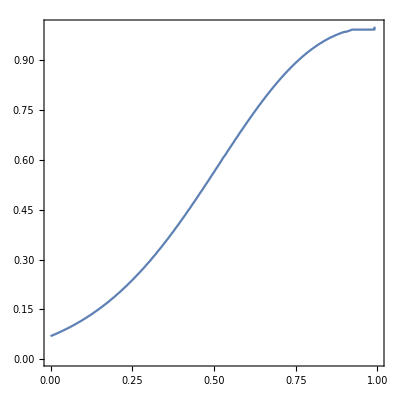

```mathematica
ContourPlot[f[X,Z]==0,{X,0,1},{Z,0,1}]
```

```mathematica
(*Plot the Einstein fixed points*)
EPts=ParametricPlot3D[{X,0,(6.+25. X+29. X^2)/(86.-135. X+109. X^2)},{X,0,1},{Z,0,1},PlotStyle->{{Thickness[0.01],Red}}];
```

```mathematica
Show[PhaseSpacexy1,PhaseSpacexy2,PhaseSpacexy3,PhaseSpacexy4,PhaseSpacexy5,PhaseSpacexy6,PhaseSpacexy7,PhaseSpacexy8,PhaseSpacexy9,PhaseSpacexy10,PhaseSpacexy11,PhaseSpacexy12,PhaseSpacexy13,PhaseSpacexy14,PhaseSpacexy15,FFSPlus,FFSMinus,AccnXYZ,EPts,PlotRange->{{0,1},{-1,1},{0,1}}]
```

-Graphics3D-

## Numeric Compact Phase Spaces: Density Parameters

```mathematica
(*Define the dynamical system for compact interacting dark matter (Z) and dark energy (X)*)
deXt:=X1'[t]==-3*(Y1[t]/((1-Y1[t]^2)^(1/2)))*(X1[t]-ℛ*(1-X1[t]))*((1+wx)*(1-X1[t])+ϵ*X1[t])-q*X1[t]*(1-X1[t])*(Z1[t]/(1-Z1[t]))*(Y1[t]/((1-Y1[t]^2)^(1/2)))
deYt:=Y1'[t]==-Y1[t]^2*(1-Y1[t]^2)^(1/2)-(((1-Y1[t]^2)^(3/2))/6)*((Z1[t]/(1-Z1[t]))+(X1[t]/(1-X1[t]))*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*X1[t]^2/((1-X1[t])^2))
deZt:=Z1'[t]==-3*Z1[t]*(1-Z1[t])*(Y1[t]/((1-Y1[t]^2)^(1/2))) + q*(X1[t]/(1-X1[t]))*Z1[t]*(1-Z1[t])*(Y1[t]/((1-Y1[t]^2)^(1/2)))
```

```mathematica
q=1;
wx=-0.5;
ϵ=-0.25;
ℛ=0.05;
α=0.5;
```

```mathematica
(*Plot the FFS*)
ffs=(1/3)*(X/(1-X)+Z/(1-Z));
FFS=Sqrt[ffs/(1+ffs)];
```

```mathematica
FFSPlus=ParametricPlot3D[{X,FFS,Z},{X,0,1},{Z,0,1},PlotStyle->{{Darker[Green],Opacity[0.25]}},Mesh->None];
FFSMinus=ParametricPlot3D[{X,-FFS,Z},{X,0,1},{Z,0,1},PlotStyle->{{Darker[Green],Opacity[0.25]}},Mesh->None];
```

```mathematica
(*Define initial conditions using the density parameters*)
Ωm0=1-Ωx0-Ωk0;
```

```mathematica
(*Flat case*)
Ωk0=0.003;
```

```mathematica
traj1[Y0_,Ωx0_]=NDSolve[{deXt,deYt,deZt, X1[0]==ℛ/(α+ℛ),Y1[0]==Y0,Z1[0]==Ωm0*ℛ/(Ωx0*α+Ωm0*ℛ)}, {X1,Y1,Z1},{t,-100,100}];
```

NDSolve::ndinnt: Initial condition Y0 is not a number or a rectangular array of numbers.

```mathematica
sol[1]=traj1[0,0.6889]
sol[2]=traj1[0,0.6889+0.0056]
sol[3]=traj1[0,0.6889-0.0056]
```

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

```mathematica
sol[4]=traj1[0.5,0.6889]
sol[5]=traj1[0.5,0.6889+0.0056]
sol[6]=traj1[0.5,0.6889-0.0056]
```

NDSolve::ndcf: Repeated convergence test failure at t == -1.76056; unable to continue.

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

Power::infy: Infinite expression 1/(√(0.+0. ⅈ)) encountered.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity encountered.

NDSolve::nlnum: The function value {Indeterminate,0.+0. ⅈ,Indeterminate} is not a list of numbers with dimensions {3} at {t,X1[t],Y1[t],Z1[t]} = {-1.76111,0.75+0. ⅈ,1.+0. ⅈ,0.42446+0. ⅈ}.

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

Power::infy: Infinite expression 1/(√(0.+0. ⅈ)) encountered.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity encountered.

NDSolve::nlnum: The function value {Indeterminate,0.+0. ⅈ,Indeterminate} is not a list of numbers with dimensions {3} at {t,X1[t],Y1[t],Z1[t]} = {-1.76002,0.75+0. ⅈ,1.+0. ⅈ,0.42446+0. ⅈ}.

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

```mathematica
sol[7]=traj1[-0.5,0.6889]
sol[8]=traj1[-0.5,0.6889+0.0056]
sol[9]=traj1[-0.5,0.6889-0.0056]
```

Power::infy: Infinite expression 1/(√(0.+0. ⅈ)) encountered.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity encountered.

NDSolve::nlnum: The function value {Indeterminate,0.+0. ⅈ,Indeterminate} is not a list of numbers with dimensions {3} at {t,X1[t],Y1[t],Z1[t]} = {1.76056,0.75+0. ⅈ,-1.+0. ⅈ,0.42446+0. ⅈ}.

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

NDSolve::mxst: Maximum number of 893183 steps reached at the point t == 1.76133.

{{X1→InterpolatingFunction[{{-100., 1.76133}}, <>],Y1→InterpolatingFunction[{{-100., 1.76133}}, <>],Z1→InterpolatingFunction[{{-100., 1.76133}}, <>]}}

Power::infy: Infinite expression 1/(√(0.+0. ⅈ)) encountered.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity encountered.

NDSolve::nlnum: The function value {Indeterminate,0.+0. ⅈ,Indeterminate} is not a list of numbers with dimensions {3} at {t,X1[t],Y1[t],Z1[t]} = {1.76002,0.75+0. ⅈ,-1.+0. ⅈ,0.42446+0. ⅈ}.

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

```mathematica
sol[10]=traj1[0.1,0.6889]
sol[11]=traj1[0.1,0.6889+0.0056]
sol[12]=traj1[0.1,0.6889-0.0056]
```

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

```mathematica
sol[13]=traj1[-0.1,0.6889]
sol[14]=traj1[-0.1,0.6889+0.0056]
sol[15]=traj1[-0.1,0.6889-0.0056]
```

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

```mathematica
sol[16]=traj1[0,0.09]
```

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

```mathematica
PhaseSpacexy1=ParametricPlot3D[Evaluate[{X1[t],Y1[t],Z1[t]}/.sol[1],{t,-100,100},PlotStyle -> {{Darker[Green], Opacity[0.75]}}],AxesLabel->{"X","Y","Z"},PlotPoints->500];
```

```mathematica
PhaseSpacexy2=ParametricPlot3D[Evaluate[{X1[t],Y1[t],Z1[t]}/.sol[2],{t,-100,100},PlotStyle -> {{Darker[Green], Opacity[0.75]}}],AxesLabel->{"X","Y","Z"},PlotPoints->500];
```

```mathematica
PhaseSpacexy3=ParametricPlot3D[Evaluate[{X1[t],Y1[t],Z1[t]}/.sol[3], {t,-100,100},PlotStyle -> {{Orange, Opacity[0.75]}}],AxesLabel->{"X","Y","Z"},PlotPoints->500];
```

```mathematica
PhaseSpacexy4=ParametricPlot3D[Evaluate[{X1[t],Y1[t],Z1[t]}/.sol[4],{t,-1.7,100},PlotStyle -> {{Orange, Opacity[0.75]}}],AxesLabel->{"X","Y","Z"},PlotPoints->500];
```

```mathematica
PhaseSpacexy5=ParametricPlot3D[Evaluate[{X1[t],Y1[t],Z1[t]}/.sol[5],{t,-1.7,100},PlotStyle -> {{Purple, Opacity[0.75]}}],AxesLabel->{"X","Y","Z"},PlotPoints->10000];
```

```mathematica
PhaseSpacexy6=ParametricPlot3D[Evaluate[{X1[t],Y1[t],Z1[t]}/.sol[6],{t,-1.7,100},PlotStyle -> {{Purple, Opacity[0.75]}}],AxesLabel->{"X","Y","Z"},PlotPoints->10000];
```

```mathematica
PhaseSpacexy7=ParametricPlot3D[Evaluate[{X1[t],Y1[t],Z1[t]}/.sol[7],{t,-100,1.7},PlotStyle -> {{Pink, Opacity[0.75]}}],PlotPoints->500,AxesLabel->{"X","Y","Z"}];
```

```mathematica
PhaseSpacexy8=ParametricPlot3D[Evaluate[{X1[t],Y1[t],Z1[t]}/.sol[8],{t,-100,1.7},PlotStyle -> {{Pink, Opacity[0.75]}}],PlotPoints->500,AxesLabel->{"X","Y","Z"}];
```

```mathematica
PhaseSpacexy9=ParametricPlot3D[Evaluate[{X1[t],Y1[t],Z1[t]}/.sol[9],{t,-100,1.7},PlotStyle -> {{Brown, Opacity[0.75]}}],PlotPoints->500,AxesLabel->{"X","Y","Z"}];
```

```mathematica
PhaseSpacexy10=ParametricPlot3D[Evaluate[{X1[t],Y1[t],Z1[t]}/.sol[10],{t,-100,100},PlotStyle -> {{Pink, Opacity[0.75]}}],PlotPoints->500,AxesLabel->{"X","Y","Z"}];
```

```mathematica
PhaseSpacexy11=ParametricPlot3D[Evaluate[{X1[t],Y1[t],Z1[t]}/.sol[11],{t,-100,100},PlotStyle -> {{Pink, Opacity[0.75]}}],PlotPoints->500,AxesLabel->{"X","Y","Z"}];
```

```mathematica
PhaseSpacexy12=ParametricPlot3D[Evaluate[{X1[t],Y1[t],Z1[t]}/.sol[12],{t,-100,100},PlotStyle -> {{Brown, Opacity[0.75]}}],PlotPoints->500,AxesLabel->{"X","Y","Z"}];
```

```mathematica
PhaseSpacexy13=ParametricPlot3D[Evaluate[{X1[t],Y1[t],Z1[t]}/.sol[13],{t,-100,100},PlotStyle -> {{Pink, Opacity[0.75]}}],PlotPoints->500,AxesLabel->{"X","Y","Z"}];
```

```mathematica
PhaseSpacexy14=ParametricPlot3D[Evaluate[{X1[t],Y1[t],Z1[t]}/.sol[14],{t,-100,100},PlotStyle -> {{Pink, Opacity[0.75]}}],PlotPoints->500,AxesLabel->{"X","Y","Z"}];
```

```mathematica
PhaseSpacexy15=ParametricPlot3D[Evaluate[{X1[t],Y1[t],Z1[t]}/.sol[15],{t,-100,100},PlotStyle -> {{Brown, Opacity[0.75]}}],PlotPoints->500,AxesLabel->{"X","Y","Z"}];
```

```mathematica
PhaseSpacexy16=ParametricPlot3D[Evaluate[{X1[t],Y1[t],Z1[t]}/.sol[16],{t,-0.13,100},PlotStyle -> {{Pink, Opacity[0.75]}}],PlotPoints->500,AxesLabel->{"X","Y","Z"}];
```

```mathematica
(*Plot the boundary between accelerating and decelerating regions*)
(*The region above this surface is accelerating, and below is decelerating*)
AccnXYZ=ContourPlot3D[-(((1-Y^2)^(3/2))/6)*((Z/(1-Z))+(X/(1-X))*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*X^2/((1-X)^2))==0,{X,0,1},{Y,-1,1},{Z,0,1},Mesh->None,ContourStyle->{Red,Opacity[0.2]}];
```

```mathematica
Show[PhaseSpacexy1,PhaseSpacexy2,PhaseSpacexy3,PhaseSpacexy4,PhaseSpacexy5,PhaseSpacexy6,PhaseSpacexy7,PhaseSpacexy8,PhaseSpacexy9,PhaseSpacexy10,PhaseSpacexy11,PhaseSpacexy12,PhaseSpacexy13,PhaseSpacexy14,PhaseSpacexy15,PhaseSpacexy16,FPsXYZ,FFSPlus,FFSMinus,AccnXYZ,PlotRange->{{0,1},{-1,1},{0,1}}]
```

-Graphics3D-

### Numeric Compact Phase Spaces : Density Parameters

```mathematica
(*Define the dynamical system for compact interacting dark matter (Z) and dark energy (X)*)
deXt:=X1'[t]==-3*(Y1[t]/((1-Y1[t]^2)^(1/2)))*(X1[t]-ℛ*(1-X1[t]))*((1+wx)*(1-X1[t])+ϵ*X1[t])-q*X1[t]*(1-X1[t])*(Z1[t]/(1-Z1[t]))*(Y1[t]/((1-Y1[t]^2)^(1/2)))
deYt:=Y1'[t]==-Y1[t]^2*(1-Y1[t]^2)^(1/2)-(((1-Y1[t]^2)^(3/2))/6)*((Z1[t]/(1-Z1[t]))+(X1[t]/(1-X1[t]))*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*X1[t]^2/((1-X1[t])^2))
deZt:=Z1'[t]==-3*Z1[t]*(1-Z1[t])*(Y1[t]/((1-Y1[t]^2)^(1/2))) + q*(X1[t]/(1-X1[t]))*Z1[t]*(1-Z1[t])*(Y1[t]/((1-Y1[t]^2)^(1/2)))
```

```mathematica
q=1;
wx=-0.5;
ϵ=-0.25;
ℛ=0.05;
α=0.5;
```

```mathematica
(*Plot the FFS*)
ffs=(1/3)*(X/(1-X)+Z/(1-Z));
FFS=Sqrt[ffs/(1+ffs)];
FFSPlus=ParametricPlot3D[{X,FFS,Z},{X,0,1},{Z,0,1},PlotStyle->{{Darker[Green],Opacity[0.25]}},Mesh->None];
FFSMinus=ParametricPlot3D[{X,-FFS,Z},{X,0,1},{Z,0,1},PlotStyle->{{Darker[Green],Opacity[0.25]}},Mesh->None];
```

```mathematica
(*Define initial conditions using the density parameters*)
Ωm0=1-Ωx0-Ωk0;
(*Flat case*)
Ωk0=-0.001;
```

```mathematica
traj1[Y0_,Ωx0_]=NDSolve[{deXt,deYt,deZt, X1[0]==ℛ/(α+ℛ),Y1[0]==Y0,Z1[0]==Ωm0*ℛ/(Ωx0*α+Ωm0*ℛ)}, {X1,Y1,Z1},{t,-100,100}];
```

NDSolve::ndinnt: Initial condition Y0 is not a number or a rectangular array of numbers.

```mathematica
Solve[Ωm0*ℛ/(Ωx0*α+Ωm0*ℛ)==0.7,Ωx0]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{Ωx0→0.0409726}}

```mathematica
sol[1]=traj1[0,0.6889]
sol[2]=traj1[0,0.6889+0.0056]
sol[3]=traj1[0,0.6889-0.0056]
```

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

```mathematica
(*sol[4]=traj1[0.5,0.6889]
sol[5]=traj1[0.5,0.6889+0.0056]
sol[6]=traj1[0.5,0.6889-0.0056]*)
```

```mathematica
(*sol[7]=traj1[-0.5,0.6889]
sol[8]=traj1[-0.5,0.6889+0.0056]
sol[9]=traj1[-0.5,0.6889-0.0056]*)
```

```mathematica
sol[10]=traj1[0.1,0.6889]
sol[11]=traj1[0.1,0.6889+0.0056]
sol[12]=traj1[0.1,0.6889-0.0056]
```

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

```mathematica
sol[13]=traj1[-0.1,0.6889]
sol[14]=traj1[-0.1,0.6889+0.0056]
sol[15]=traj1[-0.1,0.6889-0.0056]
```

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

```mathematica
sol[16]=traj1[0.2,0.6889]
sol[17]=traj1[0.1,0.6889]
sol[18]=traj1[0.4,0.6889]
```

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

NDSolve::ndcf: Repeated convergence test failure at t == -2.36187; unable to continue.

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

```mathematica
PhaseSpacexy1=ParametricPlot3D[Evaluate[{X1[t],Y1[t],Z1[t]}/.sol[1],{t,-100,100},PlotStyle -> {{Darker[Green], Opacity[0.75]}}],AxesLabel->{"X","Y","Z"},PlotPoints->500];
```

```mathematica
PhaseSpacexy2=ParametricPlot3D[Evaluate[{X1[t],Y1[t],Z1[t]}/.sol[2],{t,-100,100},PlotStyle -> {{Darker[Green], Opacity[0.75]}}],AxesLabel->{"X","Y","Z"},PlotPoints->500];
```

```mathematica
PhaseSpacexy3=ParametricPlot3D[Evaluate[{X1[t],Y1[t],Z1[t]}/.sol[3], {t,-100,100},PlotStyle -> {{Orange, Opacity[0.75]}}],AxesLabel->{"X","Y","Z"},PlotPoints->500];
```

```mathematica
(*PhaseSpacexy4=ParametricPlot3D[Evaluate[{X1[t],Y1[t],Z1[t]}/.sol[4],{t,-1.7,100},PlotStyle -> {{Orange, Opacity[0.75]}}],AxesLabel->{"X","Y","Z"},PlotPoints->500];*)
```

```mathematica
(*PhaseSpacexy5=ParametricPlot3D[Evaluate[{X1[t],Y1[t],Z1[t]}/.sol[5],{t,-1.7,100},PlotStyle -> {{Purple, Opacity[0.75]}}],AxesLabel->{"X","Y","Z"},PlotPoints->10000];*)
```

```mathematica
(*PhaseSpacexy6=ParametricPlot3D[Evaluate[{X1[t],Y1[t],Z1[t]}/.sol[6],{t,-1.7,100},PlotStyle -> {{Purple, Opacity[0.75]}}],AxesLabel->{"X","Y","Z"},PlotPoints->10000];*)
```

```mathematica
(*PhaseSpacexy7=ParametricPlot3D[Evaluate[{X1[t],Y1[t],Z1[t]}/.sol[7],{t,-100,1.7},PlotStyle -> {{Pink, Opacity[0.75]}}],PlotPoints->500,AxesLabel->{"X","Y","Z"}];*)
```

```mathematica
(*PhaseSpacexy8=ParametricPlot3D[Evaluate[{X1[t],Y1[t],Z1[t]}/.sol[8],{t,-100,1.7},PlotStyle -> {{Pink, Opacity[0.75]}}],PlotPoints->500,AxesLabel->{"X","Y","Z"}];*)
```

```mathematica
(*PhaseSpacexy9=ParametricPlot3D[Evaluate[{X1[t],Y1[t],Z1[t]}/.sol[9],{t,-100,1.7},PlotStyle -> {{Brown, Opacity[0.75]}}],PlotPoints->500,AxesLabel->{"X","Y","Z"}];*)
```

```mathematica
PhaseSpacexy10=ParametricPlot3D[Evaluate[{X1[t],Y1[t],Z1[t]}/.sol[10],{t,-100,100},PlotStyle -> {{Pink, Opacity[0.75]}}],PlotPoints->500,AxesLabel->{"X","Y","Z"}];
```

```mathematica
PhaseSpacexy11=ParametricPlot3D[Evaluate[{X1[t],Y1[t],Z1[t]}/.sol[11],{t,-100,100},PlotStyle -> {{Pink, Opacity[0.75]}}],PlotPoints->500,AxesLabel->{"X","Y","Z"}];
```

```mathematica
PhaseSpacexy12=ParametricPlot3D[Evaluate[{X1[t],Y1[t],Z1[t]}/.sol[12],{t,-100,100},PlotStyle -> {{Brown, Opacity[0.75]}}],PlotPoints->500,AxesLabel->{"X","Y","Z"}];
```

```mathematica
PhaseSpacexy13=ParametricPlot3D[Evaluate[{X1[t],Y1[t],Z1[t]}/.sol[13],{t,-100,100},PlotStyle -> {{Pink, Opacity[0.75]}}],PlotPoints->500,AxesLabel->{"X","Y","Z"}];
```

```mathematica
PhaseSpacexy14=ParametricPlot3D[Evaluate[{X1[t],Y1[t],Z1[t]}/.sol[14],{t,-100,100},PlotStyle -> {{Pink, Opacity[0.75]}}],PlotPoints->500,AxesLabel->{"X","Y","Z"}];
```

```mathematica
PhaseSpacexy15=ParametricPlot3D[Evaluate[{X1[t],Y1[t],Z1[t]}/.sol[15],{t,-100,100},PlotStyle -> {{Brown, Opacity[0.75]}}],PlotPoints->500,AxesLabel->{"X","Y","Z"}];
```

```mathematica
PhaseSpacexy16=ParametricPlot3D[Evaluate[{X1[t],Y1[t],Z1[t]}/.sol[16],{t,-100,100},PlotStyle -> {{Pink, Opacity[0.75]}}],PlotPoints->500,AxesLabel->{"X","Y","Z"}];
```

```mathematica
PhaseSpacexy17=ParametricPlot3D[Evaluate[{X1[t],Y1[t],Z1[t]}/.sol[17],{t,-100,100},PlotStyle -> {{Pink, Opacity[0.75]}}],PlotPoints->500,AxesLabel->{"X","Y","Z"}];
```

```mathematica
PhaseSpacexy18=ParametricPlot3D[Evaluate[{X1[t],Y1[t],Z1[t]}/.sol[18],{t,-2,100},PlotStyle -> {{Brown, Opacity[0.75]}}],PlotPoints->500,AxesLabel->{"X","Y","Z"}];
```

```mathematica
(*Plot the boundary between accelerating and decelerating regions*)
(*The region above this surface is accelerating, and below is decelerating*)
AccnXYZ=ContourPlot3D[-(((1-Y^2)^(3/2))/6)*((Z/(1-Z))+(X/(1-X))*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*X^2/((1-X)^2))==0,{X,0,1},{Y,-1,1},{Z,0,1},Mesh->None,ContourStyle->{Red,Opacity[0.2]}];
```

```mathematica
Show[PhaseSpacexy1,PhaseSpacexy2,PhaseSpacexy3,PhaseSpacexy10,PhaseSpacexy11,PhaseSpacexy12,PhaseSpacexy13,PhaseSpacexy14,PhaseSpacexy15,PhaseSpacexy16,PhaseSpacexy17,PhaseSpacexy18,FFSPlus,FFSMinus,AccnXYZ,PlotRange->{{0,1},{-1,1},{0,1}}]
```

-Graphics3D-

## Numeric Compact Phase Spaces: Density Parameters Constant Ωk0 (Open)

```mathematica
(*Define the dynamical system for compact interacting dark matter (Z) and dark energy (X)*)
deXt:=X1'[t]==-3*(Y1[t]/((1-Y1[t]^2)^(1/2)))*(X1[t]-ℛ*(1-X1[t]))*((1+wx)*(1-X1[t])+ϵ*X1[t])-q*X1[t]*(1-X1[t])*(Z1[t]/(1-Z1[t]))*(Y1[t]/((1-Y1[t]^2)^(1/2)))
deYt:=Y1'[t]==-Y1[t]^2*(1-Y1[t]^2)^(1/2)-(((1-Y1[t]^2)^(3/2))/6)*((Z1[t]/(1-Z1[t]))+(X1[t]/(1-X1[t]))*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*X1[t]^2/((1-X1[t])^2))
deZt:=Z1'[t]==-3*Z1[t]*(1-Z1[t])*(Y1[t]/((1-Y1[t]^2)^(1/2))) + q*(X1[t]/(1-X1[t]))*Z1[t]*(1-Z1[t])*(Y1[t]/((1-Y1[t]^2)^(1/2)))
```

```mathematica
q=1;
wx=-0.5;
ϵ=-0.25;
ℛ=0.05;
α=0.5;
```

```mathematica
(*Plot the FFS*)
ffs=(1/3)*(X/(1-X)+Z/(1-Z));
FFS=Sqrt[ffs/(1+ffs)];
```

```mathematica
FFSPlus=ParametricPlot3D[{X,FFS,Z},{X,0,1},{Z,0,1},PlotStyle->{{Darker[Green],Opacity[0.25]}},Mesh->None];
FFSMinus=ParametricPlot3D[{X,-FFS,Z},{X,0,1},{Z,0,1},PlotStyle->{{Darker[Green],Opacity[0.25]}},Mesh->None];
```

```mathematica
(*Define initial conditions using the density parameters*)
Ωm0=1-Ωx0-Ωk0;
```

```mathematica
(*Open case*)
Ωk0=0.003;
```

```mathematica
x0=ℛ/α;
```

```mathematica
z0=Ωm0*ℛ/(Ωx0*α);
```

```mathematica
K=-Ωk0*ℛ/(3*α*Ωx0)
```

-0.0001/Ωx0

```mathematica
y0=Sqrt[x0/3+z0/3-K];
```

```mathematica
traj1[Ωx0_,β_]=NDSolve[{deXt,deYt,deZt, X1[0]==x0/(1+x0),Y1[0]==β*y0/Sqrt[1+y0^2],Z1[0]==z0/(1+z0)}, {X1,Y1,Z1},{t,-100,100}];
```

NDSolve::ndinnt: Initial condition (√(0.0333333+0.0001/Ωx0+(0.0333333 (0.997-1. Ωx0))/Ωx0))/(√(1.03333+0.0001/Ωx0+(0.0333333 (0.997-1. Ωx0))/Ωx0)) is not a number or a rectangular array of numbers.

```mathematica
sol[1]=traj1[0.6889,1]
sol[2]=traj1[0.2,1]
sol[3]=traj1[0.5,1]
```

NDSolve::mxst: Maximum number of 237477 steps reached at the point t == -7.02577.

{{X1→InterpolatingFunction[{{-7.02577, 100.}}, <>],Y1→InterpolatingFunction[{{-7.02577, 100.}}, <>],Z1→InterpolatingFunction[{{-7.02577, 100.}}, <>]}}

NDSolve::mxst: Maximum number of 1277369 steps reached at the point t == -4.53301.

{{X1→InterpolatingFunction[{{-4.53301, 100.}}, <>],Y1→InterpolatingFunction[{{-4.53301, 100.}}, <>],Z1→InterpolatingFunction[{{-4.53301, 100.}}, <>]}}

NDSolve::mxst: Maximum number of 426641 steps reached at the point t == -5.85427.

{{X1→InterpolatingFunction[{{-5.85427, 100.}}, <>],Y1→InterpolatingFunction[{{-5.85427, 100.}}, <>],Z1→InterpolatingFunction[{{-5.85427, 100.}}, <>]}}

```mathematica
sol[4]=traj1[0.1,1]
sol[5]=traj1[0.3,1]
sol[6]=traj1[0.8,1]
```

NDSolve::mxst: Maximum number of 1992232 steps reached at the point t == -4.04113.

{{X1→InterpolatingFunction[{{-4.04113, 100.}}, <>],Y1→InterpolatingFunction[{{-4.04113, 100.}}, <>],Z1→InterpolatingFunction[{{-4.04113, 100.}}, <>]}}

NDSolve::mxst: Maximum number of 858299 steps reached at the point t == -6.05918.

{{X1→InterpolatingFunction[{{-6.05918, 100.}}, <>],Y1→InterpolatingFunction[{{-6.05918, 100.}}, <>],Z1→InterpolatingFunction[{{-6.05918, 100.}}, <>]}}

NDSolve::mxst: Maximum number of 175801 steps reached at the point t == -7.54688.

{{X1→InterpolatingFunction[{{-7.54688, 100.}}, <>],Y1→InterpolatingFunction[{{-7.54688, 100.}}, <>],Z1→InterpolatingFunction[{{-7.54688, 100.}}, <>]}}

```mathematica
PhaseSpacexy1=ParametricPlot3D[Evaluate[{X1[t],Y1[t],Z1[t]}/.sol[1],{t,-7,100},PlotStyle -> {{Darker[Green], Opacity[0.75]}}],AxesLabel->{"X","Y","Z"},PlotPoints->500];
```

```mathematica
PhaseSpacexy2=ParametricPlot3D[Evaluate[{X1[t],Y1[t],Z1[t]}/.sol[2],{t,-4,100},PlotStyle -> {{Darker[Green], Opacity[0.75]}}],AxesLabel->{"X","Y","Z"},PlotPoints->500];
```

```mathematica
PhaseSpacexy3=ParametricPlot3D[Evaluate[{X1[t],Y1[t],Z1[t]}/.sol[3], {t,-5,100},PlotStyle -> {{Orange, Opacity[0.75]}}],AxesLabel->{"X","Y","Z"},PlotPoints->500];
```

```mathematica
PhaseSpacexy4=ParametricPlot3D[Evaluate[{X1[t],Y1[t],Z1[t]}/.sol[4],{t,-4,100},PlotStyle -> {{Orange, Opacity[0.75]}}],AxesLabel->{"X","Y","Z"},PlotPoints->500];
```

```mathematica
PhaseSpacexy5=ParametricPlot3D[Evaluate[{X1[t],Y1[t],Z1[t]}/.sol[5],{t,-6,100},PlotStyle -> {{Purple, Opacity[0.75]}}],AxesLabel->{"X","Y","Z"},PlotPoints->10000];
```

```mathematica
PhaseSpacexy6=ParametricPlot3D[Evaluate[{X1[t],Y1[t],Z1[t]}/.sol[6],{t,-7,100},PlotStyle -> {{Purple, Opacity[0.75]}}],AxesLabel->{"X","Y","Z"},PlotPoints->10000];
```

```mathematica
(*Plot the boundary between accelerating and decelerating regions*)
(*The region above this surface is accelerating, and below is decelerating*)
AccnXYZ=ContourPlot3D[-(((1-Y^2)^(3/2))/6)*((Z/(1-Z))+(X/(1-X))*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*X^2/((1-X)^2))==0,{X,0,1},{Y,-1,1},{Z,0,1},Mesh->None,ContourStyle->{Red,Opacity[0.2]}];
```

```mathematica
Show[PhaseSpacexy1,PhaseSpacexy2,PhaseSpacexy3,PhaseSpacexy4,PhaseSpacexy5,PhaseSpacexy6,FFSPlus,FFSMinus,AccnXYZ,PlotRange->{{0,1},{-1,1},{0,1}}]
```

-Graphics3D-

## Numeric Compact Phase Spaces: Density Parameters Constant Ωk0 (Closed)

```mathematica
(*Define the dynamical system for compact interacting dark matter (Z) and dark energy (X)*)
deXt:=X1'[t]==-3*(Y1[t]/((1-Y1[t]^2)^(1/2)))*(X1[t]-ℛ*(1-X1[t]))*((1+wx)*(1-X1[t])+ϵ*X1[t])-q*X1[t]*(1-X1[t])*(Z1[t]/(1-Z1[t]))*(Y1[t]/((1-Y1[t]^2)^(1/2)))
deYt:=Y1'[t]==-Y1[t]^2*(1-Y1[t]^2)^(1/2)-(((1-Y1[t]^2)^(3/2))/6)*((Z1[t]/(1-Z1[t]))+(X1[t]/(1-X1[t]))*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*X1[t]^2/((1-X1[t])^2))
deZt:=Z1'[t]==-3*Z1[t]*(1-Z1[t])*(Y1[t]/((1-Y1[t]^2)^(1/2))) + q*(X1[t]/(1-X1[t]))*Z1[t]*(1-Z1[t])*(Y1[t]/((1-Y1[t]^2)^(1/2)))
```

```mathematica
q=1;
wx=-0.5;
ϵ=-0.25;
ℛ=0.05;
α=0.5;
```

```mathematica
(*Plot the FFS*)
ffs=(1/3)*(X/(1-X)+Z/(1-Z));
FFS=Sqrt[ffs/(1+ffs)];
```

```mathematica
FFSPlus=ParametricPlot3D[{X,FFS,Z},{X,0,1},{Z,0,1},PlotStyle->{{Darker[Green],Opacity[0.25]}},Mesh->None];
FFSMinus=ParametricPlot3D[{X,-FFS,Z},{X,0,1},{Z,0,1},PlotStyle->{{Darker[Green],Opacity[0.25]}},Mesh->None];
```

```mathematica
(*Define initial conditions using the density parameters*)
Ωm0=1-Ωx0-Ωk0;
```

```mathematica
(*Closed case*)
Ωk0=-0.001;
```

```mathematica
x0=ℛ/α;
```

```mathematica
z0=Ωm0*ℛ/(Ωx0*α);
```

```mathematica
K=-Ωk0*ℛ/(3*α*Ωx0)
```

0.0000333333/Ωx0

```mathematica
y0=Sqrt[x0/3+z0/3-K];
```

```mathematica
traj1[Ωx0_,β_]=NDSolve[{deXt,deYt,deZt, X1[0]==x0/(1+x0),Y1[0]==β*y0/Sqrt[1+y0^2],Z1[0]==z0/(1+z0)}, {X1,Y1,Z1},{t,-100,100}];
```

NDSolve::ndinnt: Initial condition (β √(0.0333333-0.0000333333/Ωx0+(0.0333333 (1.001-1. Ωx0))/Ωx0))/(√(1.03333-0.0000333333/Ωx0+(0.0333333 (1.001-1. Ωx0))/Ωx0)) is not a number or a rectangular array of numbers.

```mathematica
sol[1]=traj1[0.6889,1]
sol[2]=traj1[0.1,1]
sol[3]=traj1[0.3,1]
```

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

```mathematica
sol[4]=traj1[0.5,1]
sol[5]=traj1[0.9,1]
sol[6]=traj1[0.2,1]
```

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

```mathematica
PhaseSpacexy1=ParametricPlot3D[Evaluate[{X1[t],Y1[t],Z1[t]}/.sol[1],{t,-100,100},PlotStyle -> {{Darker[Green], Opacity[0.75]}}],AxesLabel->{"X","Y","Z"},PlotPoints->500];
```

```mathematica
PhaseSpacexy2=ParametricPlot3D[Evaluate[{X1[t],Y1[t],Z1[t]}/.sol[2],{t,-100,100},PlotStyle -> {{Darker[Green], Opacity[0.75]}}],AxesLabel->{"X","Y","Z"},PlotPoints->500];
```

```mathematica
PhaseSpacexy3=ParametricPlot3D[Evaluate[{X1[t],Y1[t],Z1[t]}/.sol[3], {t,-100,100},PlotStyle -> {{Orange, Opacity[0.75]}}],AxesLabel->{"X","Y","Z"},PlotPoints->500];
```

```mathematica
PhaseSpacexy4=ParametricPlot3D[Evaluate[{X1[t],Y1[t],Z1[t]}/.sol[4],{t,-100,100},PlotStyle -> {{Orange, Opacity[0.75]}}],AxesLabel->{"X","Y","Z"},PlotPoints->500];
```

```mathematica
PhaseSpacexy5=ParametricPlot3D[Evaluate[{X1[t],Y1[t],Z1[t]}/.sol[5],{t,-100,100},PlotStyle -> {{Purple, Opacity[0.75]}}],AxesLabel->{"X","Y","Z"},PlotPoints->10000];
```

```mathematica
PhaseSpacexy6=ParametricPlot3D[Evaluate[{X1[t],Y1[t],Z1[t]}/.sol[6],{t,-100,100},PlotStyle -> {{Purple, Opacity[0.75]}}],AxesLabel->{"X","Y","Z"},PlotPoints->10000];
```

```mathematica
(*Plot the boundary between accelerating and decelerating regions*)
(*The region above this surface is accelerating, and below is decelerating*)
AccnXYZ=ContourPlot3D[-(((1-Y^2)^(3/2))/6)*((Z/(1-Z))+(X/(1-X))*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*X^2/((1-X)^2))==0,{X,0,1},{Y,-1,1},{Z,0,1},Mesh->None,ContourStyle->{Red,Opacity[0.2]}];
```

```mathematica
Show[PhaseSpacexy1,PhaseSpacexy2,PhaseSpacexy3,PhaseSpacexy4,PhaseSpacexy5,PhaseSpacexy6,FFSPlus,FFSMinus,AccnXYZ,PlotRange->{{0,1},{-1,1},{0,1}}]
```

-Graphics3D-

## Numeric Compact Phase Spaces: Density Parameters Constant Ωk0 (Flat)

```mathematica
(*Define the dynamical system for compact interacting dark matter (Z) and dark energy (X)*)
deXt:=X1'[t]==-3*(Y1[t]/((1-Y1[t]^2)^(1/2)))*(X1[t]-ℛ*(1-X1[t]))*((1+wx)*(1-X1[t])+ϵ*X1[t])-q*X1[t]*(1-X1[t])*(Z1[t]/(1-Z1[t]))*(Y1[t]/((1-Y1[t]^2)^(1/2)))
deYt:=Y1'[t]==-Y1[t]^2*(1-Y1[t]^2)^(1/2)-(((1-Y1[t]^2)^(3/2))/6)*((Z1[t]/(1-Z1[t]))+(X1[t]/(1-X1[t]))*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*X1[t]^2/((1-X1[t])^2))
deZt:=Z1'[t]==-3*Z1[t]*(1-Z1[t])*(Y1[t]/((1-Y1[t]^2)^(1/2))) + q*(X1[t]/(1-X1[t]))*Z1[t]*(1-Z1[t])*(Y1[t]/((1-Y1[t]^2)^(1/2)))
```

```mathematica
q=1;
wx=-0.5;
ϵ=-0.25;
ℛ=0.05;
α=0.5;
```

```mathematica
(*Plot the FFS*)
ffs=(1/3)*(X/(1-X)+Z/(1-Z));
FFS=Sqrt[ffs/(1+ffs)];
```

```mathematica
FFSPlus=ParametricPlot3D[{X,FFS,Z},{X,0,1},{Z,0,1},PlotStyle->{{Darker[Green],Opacity[0.25]}},Mesh->None];
FFSMinus=ParametricPlot3D[{X,-FFS,Z},{X,0,1},{Z,0,1},PlotStyle->{{Darker[Green],Opacity[0.25]}},Mesh->None];
```

```mathematica
(*Define initial conditions using the density parameters*)
Ωm0=1-Ωx0-Ωk0;
```

```mathematica
(*Closed case*)
Ωk0=0;
```

```mathematica
x0=ℛ/α;
```

```mathematica
z0=Ωm0*ℛ/(Ωx0*α);
```

```mathematica
K=-Ωk0*ℛ/(3*α*Ωx0)
```

0.

```mathematica
y0=Sqrt[x0/3+z0/3-K];
```

```mathematica
traj1[Ωx0_,β_]=NDSolve[{deXt,deYt,deZt, X1[0]==x0/(1+x0),Y1[0]==β*y0/Sqrt[1+y0^2],Z1[0]==z0/(1+z0)}, {X1,Y1,Z1},{t,-100,100}];
```

NDSolve::ndinnt: Initial condition (β √(0.0333333+(0.0333333 (1.-1. Ωx0))/Ωx0))/(√(1.03333+(0.0333333 (1.-1. Ωx0))/Ωx0)) is not a number or a rectangular array of numbers.

```mathematica
sol[1]=traj1[0.6889,1]
sol[2]=traj1[0.6889,-1]
sol[3]=traj1[0.05,1]
```

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

NDSolve::mxst: Maximum number of 2551959 steps reached at the point t == -11.0537.

{{X1→InterpolatingFunction[{{-11.0537, 100.}}, <>],Y1→InterpolatingFunction[{{-11.0537, 100.}}, <>],Z1→InterpolatingFunction[{{-11.0537, 100.}}, <>]}}

```mathematica
sol[4]=traj1[0.05,-1]
sol[5]=traj1[0.95,1]
sol[6]=traj1[0.95,-1]
```

NDSolve::mxst: Maximum number of 2551959 steps reached at the point t == 8.25086.

{{X1→InterpolatingFunction[{{-100., 8.25086}}, <>],Y1→InterpolatingFunction[{{-100., 8.25086}}, <>],Z1→InterpolatingFunction[{{-100., 8.25086}}, <>]}}

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

```mathematica
PhaseSpacexy1=ParametricPlot3D[Evaluate[{X1[t],Y1[t],Z1[t]}/.sol[1],{t,-5,100},PlotStyle -> {{Darker[Green], Opacity[0.75]}}],AxesLabel->{"X","Y","Z"},PlotPoints->500,PlotRange->All];
```

```mathematica
PhaseSpacexy2=ParametricPlot3D[Evaluate[{X1[t],Y1[t],Z1[t]}/.sol[2],{t,-100,5},PlotStyle -> {{Darker[Green], Opacity[0.75]}}],AxesLabel->{"X","Y","Z"},PlotPoints->500];
```

```mathematica
PhaseSpacexy3=ParametricPlot3D[Evaluate[{X1[t],Y1[t],Z1[t]}/.sol[3],{t,-5,100},PlotStyle -> {{Orange, Opacity[0.75]}}],AxesLabel->{"X","Y","Z"},PlotPoints->500];
```

```mathematica
PhaseSpacexy4=ParametricPlot3D[Evaluate[{X1[t],Y1[t],Z1[t]}/.sol[4],{t,-100,5},PlotStyle -> {{Orange, Opacity[0.75]}}],AxesLabel->{"X","Y","Z"},PlotPoints->500];
```

```mathematica
PhaseSpacexy5=ParametricPlot3D[Evaluate[{X1[t],Y1[t],Z1[t]}/.sol[5],{t,-10,100},PlotStyle -> {{Purple, Opacity[0.75]}}],AxesLabel->{"X","Y","Z"},PlotPoints->500];
```

```mathematica
PhaseSpacexy6=ParametricPlot3D[Evaluate[{X1[t],Y1[t],Z1[t]}/.sol[6],{t,-100,10},PlotStyle -> {{Purple, Opacity[0.75]}}],AxesLabel->{"X","Y","Z"},PlotPoints->500];
```

```mathematica
(*Plot the boundary between accelerating and decelerating regions*)
(*The region above this surface is accelerating, and below is decelerating*)
AccnXYZ=ContourPlot3D[-(((1-Y^2)^(3/2))/6)*((Z/(1-Z))+(X/(1-X))*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*X^2/((1-X)^2))==0,{X,0,1},{Y,-1,1},{Z,0,1},Mesh->None,ContourStyle->{Red,Opacity[0.2]}];
```

```mathematica
Show[PhaseSpacexy1,PhaseSpacexy2,PhaseSpacexy3,PhaseSpacexy4,PhaseSpacexy5,PhaseSpacexy6,FFSPlus,FFSMinus,AccnXYZ,PlotRange->{{0,1},{-1,1},{0,1}}]
```

-Graphics3D-

## T-Δ System

```mathematica
deT:=T'=Simplify[-3*(Y/((1-Y^2)^(1/2)))*(X-ℛ*(1-X))*((1+wx)*(1-X)+ϵ*X)-q*X*(1-X)*(Z/(1-Z))*(Y/((1-Y^2)^(1/2)))+(-3*Z*(1-Z)*(Y/((1-Y^2)^(1/2))) + q*(X/(1-X))*Z*(1-Z)*(Y/((1-Y^2)^(1/2))))]
deΔ:=Δ'=Simplify[-3*(Y/((1-Y^2)^(1/2)))*(X-ℛ*(1-X))*((1+wx)*(1-X)+ϵ*X)-q*X*(1-X)*(Z/(1-Z))*(Y/((1-Y^2)^(1/2)))-(-3*Z*(1-Z)*(Y/((1-Y^2)^(1/2))) + q*(X/(1-X))*Z*(1-Z)*(Y/((1-Y^2)^(1/2))))]
```

```mathematica
deYt:=
Y1'[t]==-Y1[t]^2*(1-Y1[t]^2)^(1/2)-(((1-Y1[t]^2)^(3/2))/6)*((Z1[t]/(1-Z1[t]))+(X1[t]/(1-X1[t]))*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*X1[t]^2/((1-X1[t])^2))
```

```mathematica
q=1;
wx=-0.5;
ϵ=-0.25;
ℛ=0.05;
α=0.5;
```

```mathematica
Simplify[deT]/.{X->1,Z->1}
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression (0. Y ComplexInfinity ComplexInfinity)/(√(1-Y^2)) encountered.

Indeterminate

```mathematica
Simplify[deT]/.{X->1,Z->0}
```

Power::infy: Infinite expression 1/0. encountered.

ComplexInfinity

```mathematica
Simplify[deT]/.{X->0,Z->1}
```

Power::infy: Infinite expression 1/0. encountered.

ComplexInfinity